# Ejercicio I.3: Simulación de elementos de la red

## Nombre del Alumno: Felix Sanz González DNI: 78997168B

# -Graphics-

# 1.- Generacion de paquetes, y transmisiones. Abstracción de un enlace

```mathematica
Clear["Global`*"]
err = 0.1;
npaquetes = 1000;
lambda = 2000;
a = 2;

p = 0.2;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
```

1/6000

1066.67

```mathematica
RndExp[ratio_] := -Log[RandomReal[]]/ratio//N;
```

```mathematica
RndExp[lambda]
```

0.000643523

```mathematica
GetArrivals[transmisionlista_,tp_]:=Map[(If[#[[4]]==0,#[[1]]+#[[2]]+tp,Unevaluated[Sequence[]]])&,transmisionlista];
```

```mathematica
(*Source[tentrellegadas_,len_,idFlow_,period_,idIn_:0]:=*)
createPackets[lambda_,len_,idFlow_,period_,idIn_]:= 
Module[{checktime =0, n =1, lista = {idIn}},
NestWhileList[({checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime})&, 
{checktime += RndExp[lambda], RndExp[1/l],n,0,0,n++,idFlow,lista,checktime}, (#[[1]]< period)&]];
```

```mathematica
paquetes = createPackets[lambda,l,1,1,0];
paquetes[[1;;5]]
Last[paquetes]
```

{{0.000264747,2826.32,1,0,0,1,1,{0},0.000264747},{0.000320106,839.732,2,0,0,2,1,{0},0.000320106},{0.000392643,27.4807,3,0,0,3,1,{0},0.000392643},{0.00079726,104.661,4,0,0,4,1,{0},0.00079726},{0.00090017,1386.09,5,0,0,5,1,{0},0.00090017}}

{1.00003,1604.62,2060,0,0,2060,1,{0},1.00003}

```mathematica
(* pkt={chkTime,length,nseqLink,error,nrtx,nseqFlow,flowId,{path},{timePath}} *)

createTx[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
None;
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]

createTxSW[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
];

createTxGBN[paqin_,p_, tp_,c_]:=
Module[{nrtx=0,n=1,ts=0,checkTime=0,listTx},
GetPacket[pck_]:=(
listTx={};
nrtx=0;
If[pck[[1]]>checkTime,checkTime=pck[[1]]];
While[(err=If[p>RandomReal[],1,0])==1, (*Que hace si error*)
AppendTo[listTx,{checkTime,pck[[2]],n,1,nrtx++,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c+2*tp+ts);
]; (*Acaba y ya no hay error*)
AppendTo[listTx,{checkTime,pck[[2]],n,0,nrtx,pck[[6]],pck[[7]],pck[[8]],pck[[9]]}];
checkTime+=(pck[[2]]/c);n++;
listTx);

Flatten[Map[(GetPacket[#])&,paqin],1]
]
```

```mathematica
paquetesNormales = createTx[paquetes,p,TpSW,c];
```

```mathematica
paquetesNormales⟦1;;5⟧
```

{{0.000264747,2826.32,1,0,0,1,1,{0},0.000264747},{0.00148131,839.732,2,0,0,2,1,{0},0.000320106},{0.00207706,27.4807,3,0,0,3,1,{0},0.000392643},{0.00241898,104.661,4,0,0,4,1,{0},0.00079726},{0.00278502,1386.09,5,0,0,5,1,{0},0.00090017}}

```mathematica
paquetesSW = createTxSW[paquetes,p,TpSW,c];
paquetesSW[[1;;5]]
```

{{0.000264747,2826.32,1,0,0,1,1,{0},0.000264747},{0.00148131,839.732,2,0,0,2,1,{0},0.000320106},{0.00207706,27.4807,3,0,0,3,1,{0},0.000392643},{0.00241898,104.661,4,0,0,4,1,{0},0.00079726},{0.00278502,1386.09,5,0,0,5,1,{0},0.00090017}}

```mathematica
paquetesGBN = createTxGBN[paquetes,p,TpSW,c];
paquetesGBN[[1;;5]]
```

{{0.000264747,2826.32,1,0,0,1,1,{0},0.000264747},{0.00114797,839.732,2,1,0,2,1,{0},0.000320106},{0.00174372,839.732,2,1,1,2,1,{0},0.000320106},{0.00233947,839.732,2,0,2,2,1,{0},0.000320106},{0.00260189,27.4807,3,0,0,3,1,{0},0.000392643}}

```mathematica
Get["C:\\Users\\felix\\Desktop\\Todo\\U.P.V\\MASTER\\Segundo\\Asignaturas\\Rendimiento en Redes de Telecomunicacion\\Casos\\Caso I\\drawTxPRM2024.m"];
```

```mathematica
?drawTxPRM2024`*
```

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesNormales]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
```

Show::gcomb: Could not combine the graphics objects in Show[,paquetesNormales].

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesSW]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.005 en WW*)
```

Show::gcomb: Could not combine the graphics objects in Show[,paquetesSW].

```mathematica
SetIniParDraw[TpSW,0,c];
Manipulate[ GraphicsColumn[{
Show[DrawWin[ini,ww,8],Map[(DrawPacketTx[#])&,SelectPacketInWin[paquetesGBN]]]}],
{ini,0,0.1-ww},{ww,0.001,5}]
(*Poner 0.004 en WW*)
```

Show::gcomb: Could not combine the graphics objects in Show[,paquetesGBN].

```mathematica
(*Tenemos que conseguir hacer una lista de paquetes que no contenga los paquetes erroneos --> Filtrar *)
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

```mathematica
paquetesbuenosNormales = filtrarPaquetes[paquetesNormales,c,TpSW];
paquetesNormales[[1;;20]]
paquetesbuenosNormales[[1;;20]]
paquetesbuenosSW = filtrarPaquetes[paquetesSW,c,TpSW];
paquetesSW[[1;;20]]
paquetesbuenosSW[[1;;20]]
paquetesbuenosGBN = filtrarPaquetes[paquetesGBN,c,TpSW];
paquetesGBN[[1;;20]]
paquetesbuenosGBN[[1;;10]]
```

{{0.000264747,2826.32,1,0,0,1,1,{0},0.000264747},{0.00148131,839.732,2,0,0,2,1,{0},0.000320106},{0.00207706,27.4807,3,0,0,3,1,{0},0.000392643},{0.00241898,104.661,4,0,0,4,1,{0},0.00079726},{0.00278502,1386.09,5,0,0,5,1,{0},0.00090017},{0.0035515,925.269,6,0,0,6,1,{0},0.00121035},{0.00417398,689.445,7,0,0,7,1,{0},0.00139957},{0.00472277,1102.45,8,0,0,8,1,{0},0.00154436},{0.00540062,80.0151,9,0,0,9,1,{0},0.002269},{0.00575895,321.811,10,0,0,10,1,{0},0.00254571},{0.00619285,519.591,11,0,0,11,1,{0},0.00287691},{0.00668856,921.323,12,0,0,12,1,{0},0.00317724},{0.0073098,870.445,13,0,0,13,1,{0},0.00395101},{0.00791515,1306.,14,0,0,14,1,{0},0.0045812},{0.00865661,218.359,15,0,0,15,1,{0},0.00461896},{0.00905818,549.289,16,0,0,16,1,{0},0.00479578},{0.00956317,100.622,17,0,0,17,1,{0},0.00574842},{0.00992794,4839.03,18,0,0,18,1,{0},0.00597635},{0.0117735,333.059,19,0,0,19,1,{0},0.00649698},{0.0122109,376.666,20,0,0,20,1,{0},0.0079368}}

{{0.00131464,2826.32,1,0,0,1,1,{0},0.000264747},{0.00191039,839.732,2,0,0,2,1,{0},0.000320106},{0.00225231,27.4807,3,0,0,3,1,{0},0.000392643},{0.00261835,104.661,4,0,0,4,1,{0},0.00079726},{0.00338484,1386.09,5,0,0,5,1,{0},0.00090017},{0.00400732,925.269,6,0,0,6,1,{0},0.00121035},{0.0045561,689.445,7,0,0,7,1,{0},0.00139957},{0.00523395,1102.45,8,0,0,8,1,{0},0.00154436},{0.00559229,80.0151,9,0,0,9,1,{0},0.002269},{0.00602619,321.811,10,0,0,10,1,{0},0.00254571},{0.00652189,519.591,11,0,0,11,1,{0},0.00287691},{0.00714314,921.323,12,0,0,12,1,{0},0.00317724},{0.00774849,870.445,13,0,0,13,1,{0},0.00395101},{0.00848994,1306.,14,0,0,14,1,{0},0.0045812},{0.00889151,218.359,15,0,0,15,1,{0},0.00461896},{0.0093965,549.289,16,0,0,16,1,{0},0.00479578},{0.00976128,100.622,17,0,0,17,1,{0},0.00574842},{0.0116068,4839.03,18,0,0,18,1,{0},0.00597635},{0.0120442,333.059,19,0,0,19,1,{0},0.00649698},{0.0124953,376.666,20,0,0,20,1,{0},0.0079368}}

{{0.000264747,2826.32,1,0,0,1,1,{0},0.000264747},{0.00148131,839.732,2,0,0,2,1,{0},0.000320106},{0.00207706,27.4807,3,0,0,3,1,{0},0.000392643},{0.00241898,104.661,4,0,0,4,1,{0},0.00079726},{0.00278502,1386.09,5,0,0,5,1,{0},0.00090017},{0.0035515,925.269,6,1,0,6,1,{0},0.00121035},{0.00417398,925.269,6,1,1,6,1,{0},0.00121035},{0.00479646,925.269,6,1,2,6,1,{0},0.00121035},{0.00541894,925.269,6,0,3,6,1,{0},0.00121035},{0.00604142,689.445,7,0,0,7,1,{0},0.00139957},{0.00659021,1102.45,8,0,0,8,1,{0},0.00154436},{0.00726806,80.0151,9,0,0,9,1,{0},0.002269},{0.00762639,321.811,10,0,0,10,1,{0},0.00254571},{0.00806029,519.591,11,0,0,11,1,{0},0.00287691},{0.008556,921.323,12,0,0,12,1,{0},0.00317724},{0.00917724,870.445,13,0,0,13,1,{0},0.00395101},{0.00978259,1306.,14,0,0,14,1,{0},0.0045812},{0.0105241,218.359,15,1,0,15,1,{0},0.00461896},{0.0109256,218.359,15,0,1,15,1,{0},0.00461896},{0.0113272,549.289,16,0,0,16,1,{0},0.00479578}}

{{0.00131464,2826.32,1,0,0,1,1,{0},0.000264747},{0.00191039,839.732,2,0,0,2,1,{0},0.000320106},{0.00225231,27.4807,3,0,0,3,1,{0},0.000392643},{0.00261835,104.661,4,0,0,4,1,{0},0.00079726},{0.00338484,1386.09,5,0,0,5,1,{0},0.00090017},{0.00587476,925.269,6,0,3,6,1,{0},0.00121035},{0.00642354,689.445,7,0,0,7,1,{0},0.00139957},{0.00710139,1102.45,8,0,0,8,1,{0},0.00154436},{0.00745973,80.0151,9,0,0,9,1,{0},0.002269},{0.00789363,321.811,10,0,0,10,1,{0},0.00254571},{0.00838933,519.591,11,0,0,11,1,{0},0.00287691},{0.00901058,921.323,12,0,0,12,1,{0},0.00317724},{0.00961593,870.445,13,0,0,13,1,{0},0.00395101},{0.0103574,1306.,14,0,0,14,1,{0},0.0045812},{0.0111605,218.359,15,0,1,15,1,{0},0.00461896},{0.0116655,549.289,16,0,0,16,1,{0},0.00479578},{0.0123951,100.622,17,0,1,17,1,{0},0.00574842},{0.0142406,4839.03,18,0,0,18,1,{0},0.00597635},{0.014678,333.059,19,0,0,19,1,{0},0.00649698},{0.0155801,376.666,20,0,1,20,1,{0},0.0079368}}

{{0.000264747,2826.32,1,0,0,1,1,{0},0.000264747},{0.00114797,839.732,2,1,0,2,1,{0},0.000320106},{0.00174372,839.732,2,1,1,2,1,{0},0.000320106},{0.00233947,839.732,2,0,2,2,1,{0},0.000320106},{0.00260189,27.4807,3,0,0,3,1,{0},0.000392643},{0.00261048,104.661,4,0,0,4,1,{0},0.00079726},{0.00264318,1386.09,5,0,0,5,1,{0},0.00090017},{0.00307634,925.269,6,0,0,6,1,{0},0.00121035},{0.00336548,689.445,7,1,0,7,1,{0},0.00139957},{0.00391427,689.445,7,0,1,7,1,{0},0.00139957},{0.00412972,1102.45,8,0,0,8,1,{0},0.00154436},{0.00447423,80.0151,9,0,0,9,1,{0},0.002269},{0.00449924,321.811,10,0,0,10,1,{0},0.00254571},{0.0045998,519.591,11,0,0,11,1,{0},0.00287691},{0.00476218,921.323,12,0,0,12,1,{0},0.00317724},{0.00505009,870.445,13,0,0,13,1,{0},0.00395101},{0.0053221,1306.,14,0,0,14,1,{0},0.0045812},{0.00573023,218.359,15,0,0,15,1,{0},0.00461896},{0.00579846,549.289,16,1,0,16,1,{0},0.00479578},{0.00630345,549.289,16,0,1,16,1,{0},0.00479578}}

{{0.00131464,2826.32,1,0,0,1,1,{0},0.000264747},{0.00276856,839.732,2,0,2,2,1,{0},0.000320106},{0.00277714,27.4807,3,0,0,3,1,{0},0.000392643},{0.00280985,104.661,4,0,0,4,1,{0},0.00079726},{0.003243,1386.09,5,0,0,5,1,{0},0.00090017},{0.00353215,925.269,6,0,0,6,1,{0},0.00121035},{0.00429639,689.445,7,0,1,7,1,{0},0.00139957},{0.0046409,1102.45,8,0,0,8,1,{0},0.00154436},{0.0046659,80.0151,9,0,0,9,1,{0},0.002269},{0.00476647,321.811,10,0,0,10,1,{0},0.00254571}}

# 2 y 3.- Abstracción de un nodo de conmutación. Funciones de filtrado y multiplexado de paquetes.

Debemos implementar una función que nos permita eliminar los paquetes que contienen error, segun el campo de paquete que indica si es un paquete con error

```mathematica
(*Esta funcion tambien se encargará de actualizar el tiempo de llegada del paquete*)

filtrarPaquetes[paquetes_,c_,Tp_]:=Map[
(If[#[[4]] == 0,{#[[1]]+#[[2]]/c+Tp, #[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[8]],#[[9]]},Nothing])
&,paquetes]
```

Debemos implementar una función que nos permita dividir y conmutar  el trafico entrante a un nodo por sus distintos enlaces de salida. 
Está función tiene como parámetros de entrada la lista de paquetes, las probabilidades de los enlaces de salida y los enlaces de salida

```mathematica
(*Esta funcion da error y NO SE USA*)
Node1[in_,probs_]:=Module[{cumulativeProbs,outcomes,nProbs,nGroups,r,assignedGroups},(*Verificar que las probabilidades sumen 1*)If[Total[probs]!=1,Return["Error: La suma de las probabilidades debe ser 1."]];
(*Calcular los límites acumulados de las probabilidades*)
cumulativeProbs=Accumulate[probs];
(*Número de probabilidades y número de grupos*)
nProbs=Length[probs];
nGroups=nProbs;
(*Asignar cada elemento de'in' a un grupo según probabilidades acumuladas*)
assignedGroups=Map[With[{r=RandomReal[]},FirstPosition[cumulativeProbs,_?(#>=r&)][[1]],in];
(*Mostrar valores aleatorios y asignaciones para depuración*)
Print["Valores aleatorios: ",r,Length[in]]];
Print["Grupos asignados: ",assignedGroups];
(*Crear la lista de resultados agrupados*)
outcomes=Table[Select[Transpose[{in,assignedGroups}],#[[2]]==i+1&][[All,1]],{i,1,Length[probs]}];
(*Devolver los resultados agrupados por etiquetas*)
outcomes]
```

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId} *)
(*Esta es la función que se usa*)

Node2[in_,prob_]:=Reap[
Map[
If[RandomReal[]<prob,Sow[#,1],Sow[#,2]]&,in],
_,#2&][[2]];
```

Debemos implementar una función que nos permita multiplexar el trafico entrante a un nodo, para asi obtener una unica lista, ordenada segun el instante de llegada de cada paquete.

```mathematica
(* pkt={chkTime,length,nseqFlow,error,nrtx,nseqLink,flowId,{path} *)
Multiplexar[in_,idNodo_]:=Module[{aux={},aux2={},nodes={},times={}},
aux=Flatten[in,1]; (*Concatenar listas de paquetes en una sola lista*)
aux=SortBy[aux,#[[1]]&]; (*Ordenar la nueva lista en base al tiempo en el que han llegado los paquetes al nodo*)
Map[{

nodes=#[[8]];(*Extraer los nodos por los que ha pasado el paquete actual*)
AppendTo[nodes,idNodo]; (*Agregar el nodo actual a la lista de nodos por los que ha pasado el paquete actual*)

AppendTo[aux2,{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],nodes,#[[9]]}]}&,aux]; (*Crea la nueva lista de paquetes*)
	aux2
];
```

```mathematica
{enlace1,enlace2}= Node2[paquetesbuenosNormales[[1;;15]],0.5];
Flatten[{enlace1,enlace2},1]
enlace1
enlace2
```

{{0.00131464,2826.32,1,0,0,1,1,{0},0.000264747},{0.00225231,27.4807,3,0,0,3,1,{0},0.000392643},{0.00261835,104.661,4,0,0,4,1,{0},0.00079726},{0.00338484,1386.09,5,0,0,5,1,{0},0.00090017},{0.00400732,925.269,6,0,0,6,1,{0},0.00121035},{0.0045561,689.445,7,0,0,7,1,{0},0.00139957},{0.00523395,1102.45,8,0,0,8,1,{0},0.00154436},{0.00559229,80.0151,9,0,0,9,1,{0},0.002269},{0.00602619,321.811,10,0,0,10,1,{0},0.00254571},{0.00652189,519.591,11,0,0,11,1,{0},0.00287691},{0.00774849,870.445,13,0,0,13,1,{0},0.00395101},{0.00889151,218.359,15,0,0,15,1,{0},0.00461896},{0.00191039,839.732,2,0,0,2,1,{0},0.000320106},{0.00714314,921.323,12,0,0,12,1,{0},0.00317724},{0.00848994,1306.,14,0,0,14,1,{0},0.0045812}}

{{0.00131464,2826.32,1,0,0,1,1,{0},0.000264747},{0.00225231,27.4807,3,0,0,3,1,{0},0.000392643},{0.00261835,104.661,4,0,0,4,1,{0},0.00079726},{0.00338484,1386.09,5,0,0,5,1,{0},0.00090017},{0.00400732,925.269,6,0,0,6,1,{0},0.00121035},{0.0045561,689.445,7,0,0,7,1,{0},0.00139957},{0.00523395,1102.45,8,0,0,8,1,{0},0.00154436},{0.00559229,80.0151,9,0,0,9,1,{0},0.002269},{0.00602619,321.811,10,0,0,10,1,{0},0.00254571},{0.00652189,519.591,11,0,0,11,1,{0},0.00287691},{0.00774849,870.445,13,0,0,13,1,{0},0.00395101},{0.00889151,218.359,15,0,0,15,1,{0},0.00461896}}

{{0.00191039,839.732,2,0,0,2,1,{0},0.000320106},{0.00714314,921.323,12,0,0,12,1,{0},0.00317724},{0.00848994,1306.,14,0,0,14,1,{0},0.0045812}}

```mathematica
in2 = Multiplexar[{enlace1,enlace2},A]
```

{{0.00131464,2826.32,1,0,0,1,1,{0,A},0.000264747},{0.00191039,839.732,2,0,0,2,1,{0,A},0.000320106},{0.00225231,27.4807,3,0,0,3,1,{0,A},0.000392643},{0.00261835,104.661,4,0,0,4,1,{0,A},0.00079726},{0.00338484,1386.09,5,0,0,5,1,{0,A},0.00090017},{0.00400732,925.269,6,0,0,6,1,{0,A},0.00121035},{0.0045561,689.445,7,0,0,7,1,{0,A},0.00139957},{0.00523395,1102.45,8,0,0,8,1,{0,A},0.00154436},{0.00559229,80.0151,9,0,0,9,1,{0,A},0.002269},{0.00602619,321.811,10,0,0,10,1,{0,A},0.00254571},{0.00652189,519.591,11,0,0,11,1,{0,A},0.00287691},{0.00714314,921.323,12,0,0,12,1,{0,A},0.00317724},{0.00774849,870.445,13,0,0,13,1,{0,A},0.00395101},{0.00848994,1306.,14,0,0,14,1,{0,A},0.0045812},{0.00889151,218.359,15,0,0,15,1,{0,A},0.00461896}}

```mathematica
(*Esta funcion permite añadir numeros de secuencia a los paquetes de un flujo, es decir, a los paquetes que ya se sabe que van por un enlace*)
añadirNumSec[lista_,max_]:=Table[Append[lista[[i]],Mod[i-1,max]],{i,1,Length[lista]}]
```

```mathematica
añadirNumSec[enlace1,4]
```

{{0.00131464,2826.32,1,0,0,1,1,{0},0.000264747,0},{0.00225231,27.4807,3,0,0,3,1,{0},0.000392643,1},{0.00261835,104.661,4,0,0,4,1,{0},0.00079726,2},{0.00338484,1386.09,5,0,0,5,1,{0},0.00090017,3},{0.00400732,925.269,6,0,0,6,1,{0},0.00121035,0},{0.0045561,689.445,7,0,0,7,1,{0},0.00139957,1},{0.00523395,1102.45,8,0,0,8,1,{0},0.00154436,2},{0.00559229,80.0151,9,0,0,9,1,{0},0.002269,3},{0.00602619,321.811,10,0,0,10,1,{0},0.00254571,0},{0.00652189,519.591,11,0,0,11,1,{0},0.00287691,1},{0.00774849,870.445,13,0,0,13,1,{0},0.00395101,2},{0.00889151,218.359,15,0,0,15,1,{0},0.00461896,3}}

# 4A.- Simulación de transmisión de paquetes en la topología de red SIN protocolo

```mathematica
SetAttributes[createPrimitive,HoldAll];
MakeBoxes[Interpretation[expr,p]]//DisplayForm;
InterpretationBox["expr",p]//DisplayForm;
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]];

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
arrow=Graphics[face[0.01]];
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

-Graphics-

```mathematica
err = 0.1;
npaquetes = 250;
lambda = 2000;
a = 2;
period = 1;

p = 0.25;
mu = 3000;
TiSW = 1/mu;
TpSW =(a*TiSW-TiSW)/2 
c = 3200000;
l = c/mu//N
prob1 = 1/4;
prob2 = 1/3;
prob5 = 1/2;
```

1/6000

1066.67

```mathematica
in1 = createPackets[lambda,l,1,period,"Ori-1"];
Last[in1]
in5 = createPackets[lambda,l,1,period,"Ori-5"];
Last[in5]
in2 = createPackets[lambda,l,1,period,"Ori-2"];
Last[in2]
in1[[1;;15]];
totalin = Length[in1]+Length[in5]+Length[in2]
```

{1.00152,1484.66,1990,0,0,1990,1,{Ori-1},1.00152}

{1.0012,353.37,1952,0,0,1952,1,{Ori-5},1.0012}

{1.00007,945.436,1985,0,0,1985,1,{Ori-2},1.00007}

5927

```mathematica
{paquetes12,paquetes15} =Node2[in1,prob1];

paquetes12[[1;;15]]
paquetes15[[1;;15]]
Length[paquetes12];
Length[paquetes15];
Length[paquetes12]/(Length[paquetes15]+Length[paquetes12])//N
```

{{0.000542456,719.346,1,0,0,1,1,{Ori-1},0.000542456},{0.000587855,28.6093,2,0,0,2,1,{Ori-1},0.000587855},{0.00143565,45.63,3,0,0,3,1,{Ori-1},0.00143565},{0.0018166,182.287,4,0,0,4,1,{Ori-1},0.0018166},{0.00224395,635.597,5,0,0,5,1,{Ori-1},0.00224395},{0.00280936,301.906,6,0,0,6,1,{Ori-1},0.00280936},{0.00301138,1106.37,7,0,0,7,1,{Ori-1},0.00301138},{0.00348862,771.445,10,0,0,10,1,{Ori-1},0.00348862},{0.00476837,97.1032,12,0,0,12,1,{Ori-1},0.00476837},{0.00519356,152.985,13,0,0,13,1,{Ori-1},0.00519356},{0.00548695,790.911,14,0,0,14,1,{Ori-1},0.00548695},{0.00634217,82.3056,15,0,0,15,1,{Ori-1},0.00634217},{0.00688855,457.416,16,0,0,16,1,{Ori-1},0.00688855},{0.00718849,42.3144,18,0,0,18,1,{Ori-1},0.00718849},{0.00772386,613.073,19,0,0,19,1,{Ori-1},0.00772386}}

{{0.00329912,1208.83,8,0,0,8,1,{Ori-1},0.00329912},{0.00342104,2151.3,9,0,0,9,1,{Ori-1},0.00342104},{0.00363863,140.467,11,0,0,11,1,{Ori-1},0.00363863},{0.00704325,931.406,17,0,0,17,1,{Ori-1},0.00704325},{0.0103223,2384.16,22,0,0,22,1,{Ori-1},0.0103223},{0.0202968,937.03,34,0,0,34,1,{Ori-1},0.0202968},{0.0215714,439.229,36,0,0,36,1,{Ori-1},0.0215714},{0.022508,754.729,39,0,0,39,1,{Ori-1},0.022508},{0.0234787,2775.59,40,0,0,40,1,{Ori-1},0.0234787},{0.0252161,3403.47,47,0,0,47,1,{Ori-1},0.0252161},{0.0257367,5002.69,49,0,0,49,1,{Ori-1},0.0257367},{0.0305331,1794.81,57,0,0,57,1,{Ori-1},0.0305331},{0.030836,5941.5,58,0,0,58,1,{Ori-1},0.030836},{0.0311939,643.726,59,0,0,59,1,{Ori-1},0.0311939},{0.0325354,363.497,61,0,0,61,1,{Ori-1},0.0325354}}

0.753769

```mathematica
tx12 = createTx[paquetes12,p,TpSW,c];
tx15 = createTx[paquetes15,p,TpSW,c];
```

```mathematica
tx15[[1;;10]]
in5[[1;;10]]

inOKtx15 = filtrarPaquetes[tx15,c,TpSW];

intotal5= Multiplexar[{in5,inOKtx15},5];
intotal5[[1;;10]]

{paquetes52,paquetes54} = Node2[intotal5,prob5];
tx52 = createTx[paquetes52,p,TpSW,c];
tx54 = createTx[paquetes54,p,TpSW,c];
```

{{0.00329912,1208.83,1,0,0,8,1,{Ori-1},0.00329912},{0.00401021,2151.3,2,0,0,9,1,{Ori-1},0.00342104},{0.00501583,140.467,3,0,0,11,1,{Ori-1},0.00363863},{0.00704325,931.406,4,0,0,17,1,{Ori-1},0.00704325},{0.0103223,2384.16,5,0,0,22,1,{Ori-1},0.0103223},{0.0202968,937.03,6,0,0,34,1,{Ori-1},0.0202968},{0.0215714,439.229,7,0,0,36,1,{Ori-1},0.0215714},{0.022508,754.729,8,0,0,39,1,{Ori-1},0.022508},{0.0234787,2775.59,9,0,0,40,1,{Ori-1},0.0234787},{0.0252161,3403.47,10,0,0,47,1,{Ori-1},0.0252161}}

{{0.000375091,482.356,1,0,0,1,1,{Ori-5},0.000375091},{0.000972898,1166.41,2,0,0,2,1,{Ori-5},0.000972898},{0.00111475,2497.03,3,0,0,3,1,{Ori-5},0.00111475},{0.00130401,139.539,4,0,0,4,1,{Ori-5},0.00130401},{0.00239956,1049.88,5,0,0,5,1,{Ori-5},0.00239956},{0.00293411,344.263,6,0,0,6,1,{Ori-5},0.00293411},{0.00377039,393.864,7,0,0,7,1,{Ori-5},0.00377039},{0.00426155,949.5,8,0,0,8,1,{Ori-5},0.00426155},{0.00426981,75.4435,9,0,0,9,1,{Ori-5},0.00426981},{0.00473024,98.0618,10,0,0,10,1,{Ori-5},0.00473024}}

{{0.000375091,482.356,1,0,0,1,1,{Ori-5,5},0.000375091},{0.000972898,1166.41,2,0,0,2,1,{Ori-5,5},0.000972898},{0.00111475,2497.03,3,0,0,3,1,{Ori-5,5},0.00111475},{0.00130401,139.539,4,0,0,4,1,{Ori-5,5},0.00130401},{0.00239956,1049.88,5,0,0,5,1,{Ori-5,5},0.00239956},{0.00293411,344.263,6,0,0,6,1,{Ori-5,5},0.00293411},{0.00377039,393.864,7,0,0,7,1,{Ori-5,5},0.00377039},{0.00384355,1208.83,1,0,0,8,1,{Ori-1,5},0.00329912},{0.00426155,949.5,8,0,0,8,1,{Ori-5,5},0.00426155},{0.00426981,75.4435,9,0,0,9,1,{Ori-5,5},0.00426981}}

```mathematica
inOKtx12 = filtrarPaquetes[tx12,c,TpSW];
inOKtx52 = filtrarPaquetes[tx52,c,TpSW];
intotal2 = Multiplexar[{in2,inOKtx52, inOKtx12},2];
in2[[1;;10]]
inOKtx52[[1;;10]]
inOKtx12[[1;;10]]
intotal2[[1;;10]]
```

{{0.000525996,866.077,1,0,0,1,1,{Ori-2},0.000525996},{0.000635035,202.35,2,0,0,2,1,{Ori-2},0.000635035},{0.000639427,5262.34,3,0,0,3,1,{Ori-2},0.000639427},{0.00104718,811.525,4,0,0,4,1,{Ori-2},0.00104718},{0.00116275,2180.03,5,0,0,5,1,{Ori-2},0.00116275},{0.00167278,296.084,6,0,0,6,1,{Ori-2},0.00167278},{0.00202476,635.882,7,0,0,7,1,{Ori-2},0.00202476},{0.00204107,1689.31,8,0,0,8,1,{Ori-2},0.00204107},{0.00228861,905.106,9,0,0,9,1,{Ori-2},0.00228861},{0.0022931,11.3113,10,0,0,10,1,{Ori-2},0.0022931}}

{{0.000692493,482.356,1,0,0,1,1,{Ori-5,5},0.000375091},{0.00206174,2497.03,2,0,0,3,1,{Ori-5,5},0.00111475},{0.00243868,139.539,3,0,0,4,1,{Ori-5,5},0.00130401},{0.00438797,1208.83,4,0,0,8,1,{Ori-1,5},0.00329912},{0.00492755,98.0618,5,0,0,10,1,{Ori-5,5},0.00473024},{0.00593316,2151.3,6,0,0,9,1,{Ori-1,5},0.00342104},{0.00816084,1749.24,7,0,0,12,1,{Ori-5,5},0.00744754},{0.00878524,931.406,8,0,0,17,1,{Ori-1,5},0.00704325},{0.00961459,1587.25,9,0,0,13,1,{Ori-5,5},0.00780671},{0.0102031,585.491,10,0,0,15,1,{Ori-5,5},0.00985347}}

{{0.000933918,719.346,1,0,0,1,1,{Ori-1},0.000542456},{0.00127619,28.6093,2,0,0,2,1,{Ori-1},0.000587855},{0.00162378,45.63,3,0,0,3,1,{Ori-1},0.00143565},{0.00204023,182.287,4,0,0,4,1,{Ori-1},0.0018166},{0.00260925,635.597,5,0,0,5,1,{Ori-1},0.00224395},{0.00307038,301.906,6,0,0,6,1,{Ori-1},0.00280936},{0.00374945,1106.37,7,0,0,7,1,{Ori-1},0.00301138},{0.00432386,771.445,8,0,0,10,1,{Ori-1},0.00348862},{0.00496538,97.1032,9,0,0,12,1,{Ori-1},0.00476837},{0.00540803,152.985,10,0,0,13,1,{Ori-1},0.00519356}}

{{0.000525996,866.077,1,0,0,1,1,{Ori-2,2},0.000525996},{0.000635035,202.35,2,0,0,2,1,{Ori-2,2},0.000635035},{0.000639427,5262.34,3,0,0,3,1,{Ori-2,2},0.000639427},{0.000692493,482.356,1,0,0,1,1,{Ori-5,5,2},0.000375091},{0.000933918,719.346,1,0,0,1,1,{Ori-1,2},0.000542456},{0.00104718,811.525,4,0,0,4,1,{Ori-2,2},0.00104718},{0.00116275,2180.03,5,0,0,5,1,{Ori-2,2},0.00116275},{0.00127619,28.6093,2,0,0,2,1,{Ori-1,2},0.000587855},{0.00162378,45.63,3,0,0,3,1,{Ori-1,2},0.00143565},{0.00167278,296.084,6,0,0,6,1,{Ori-2,2},0.00167278}}

```mathematica
{paquetes23,paquetes24} = Node2[intotal2,prob2];

tx23 = createTx[paquetes23,p,TpSW,c];
tx24 = createTx[paquetes24,p,TpSW,c];
```

```mathematica
inOK3 = filtrarPaquetes[tx23,c,TpSW];
out3 = Multiplexar[{inOK3},3];
out3[[1;;10]]
```

{{0.000963312,866.077,1,0,0,1,1,{Ori-2,2,3},0.000525996},{0.00135988,202.35,2,0,0,2,1,{Ori-2,2,3},0.000635035},{0.00333769,5262.34,3,0,0,3,1,{Ori-2,2,3},0.000639427},{0.00382176,482.356,4,0,0,1,1,{Ori-5,5,2,3},0.000375091},{0.0044087,811.525,5,0,0,4,1,{Ori-2,2,3},0.00104718},{0.00475097,28.6093,6,0,0,2,1,{Ori-1,2,3},0.000587855},{0.00517683,296.084,7,0,0,6,1,{Ori-2,2,3},0.00167278},{0.00570888,635.882,8,0,0,7,1,{Ori-2,2,3},0.00202476},{0.00609918,182.287,9,0,0,4,1,{Ori-1,2,3},0.0018166},{0.00671536,905.106,10,0,0,9,1,{Ori-2,2,3},0.00228861}}

```mathematica
inOKtx54 = filtrarPaquetes[tx54,c,TpSW];
inOKtx24 = filtrarPaquetes[tx24,c,TpSW];
intotal4 = Multiplexar[{inOKtx54, inOKtx24},4];
inOKtx54[[1;;10]]
inOKtx24[[1;;10]]
intotal4[[1;;10]]
```

{{0.00150407,1166.41,1,0,0,2,1,{Ori-5,5},0.000972898},{0.00289432,1049.88,2,0,0,5,1,{Ori-5,5},0.00239956},{0.00333523,344.263,3,0,0,6,1,{Ori-5,5},0.00293411},{0.00406014,393.864,4,0,0,7,1,{Ori-5,5},0.00377039},{0.00472493,949.5,5,0,0,8,1,{Ori-5,5},0.00426155},{0.00508184,75.4435,6,0,0,9,1,{Ori-5,5},0.00426981},{0.00545907,140.467,7,0,0,11,1,{Ori-1,5},0.00363863},{0.00644411,1420.56,8,0,0,11,1,{Ori-5,5},0.00583352},{0.00947509,571.863,9,0,0,14,1,{Ori-5,5},0.00912972},{0.0103323,42.6043,10,0,0,16,1,{Ori-5,5},0.0101523}}

{{0.00132538,719.346,1,0,0,1,1,{Ori-1,2},0.000542456},{0.00233997,2180.03,2,0,0,5,1,{Ori-2,2},0.00116275},{0.00268756,45.63,3,0,0,3,1,{Ori-1,2},0.00143565},{0.00354881,1689.31,4,0,0,8,1,{Ori-2,2},0.00204107},{0.00466246,2497.03,5,0,0,3,1,{Ori-5,5,2},0.00111475},{0.0050394,139.539,6,0,0,4,1,{Ori-5,5,2},0.00130401},{0.00546708,301.906,7,0,0,6,1,{Ori-1,2},0.00280936},{0.00614615,1106.37,8,0,0,7,1,{Ori-1,2},0.00301138},{0.00672056,771.445,9,0,0,10,1,{Ori-1,2},0.00348862},{0.00708454,98.0618,10,0,0,10,1,{Ori-5,5,2},0.00473024}}

{{0.00132538,719.346,1,0,0,1,1,{Ori-1,2,4},0.000542456},{0.00150407,1166.41,1,0,0,2,1,{Ori-5,5,4},0.000972898},{0.00233997,2180.03,2,0,0,5,1,{Ori-2,2,4},0.00116275},{0.00268756,45.63,3,0,0,3,1,{Ori-1,2,4},0.00143565},{0.00289432,1049.88,2,0,0,5,1,{Ori-5,5,4},0.00239956},{0.00333523,344.263,3,0,0,6,1,{Ori-5,5,4},0.00293411},{0.00354881,1689.31,4,0,0,8,1,{Ori-2,2,4},0.00204107},{0.00406014,393.864,4,0,0,7,1,{Ori-5,5,4},0.00377039},{0.00466246,2497.03,5,0,0,3,1,{Ori-5,5,2,4},0.00111475},{0.00472493,949.5,5,0,0,8,1,{Ori-5,5,4},0.00426155}}

```mathematica
out4 = intotal4;
out4[[1;;10]]
```

{{0.00132538,719.346,1,0,0,1,1,{Ori-1,2,4},0.000542456},{0.00150407,1166.41,1,0,0,2,1,{Ori-5,5,4},0.000972898},{0.00233997,2180.03,2,0,0,5,1,{Ori-2,2,4},0.00116275},{0.00268756,45.63,3,0,0,3,1,{Ori-1,2,4},0.00143565},{0.00289432,1049.88,2,0,0,5,1,{Ori-5,5,4},0.00239956},{0.00333523,344.263,3,0,0,6,1,{Ori-5,5,4},0.00293411},{0.00354881,1689.31,4,0,0,8,1,{Ori-2,2,4},0.00204107},{0.00406014,393.864,4,0,0,7,1,{Ori-5,5,4},0.00377039},{0.00466246,2497.03,5,0,0,3,1,{Ori-5,5,2,4},0.00111475},{0.00472493,949.5,5,0,0,8,1,{Ori-5,5,4},0.00426155}}

```mathematica
totalout = Length[out3]+Length[out4]
```

5927

# 5A.- Simulación de transmisión de paquetes en la topología de red CON protocolo S&W:

```mathematica
in1SW = createPackets[lambda,l,1,period,"Ori-1"];
in5SW = createPackets[lambda,l,1,period,"Ori-5"];
in2SW = createPackets[lambda,l,1,period,"Ori-2"];
in1SW[[1;;15]];
totalinSW = Length[in1SW]+Length[in5SW]+Length[in2SW]
```

5982

```mathematica
{paquetes12SW,paquetes15SW} =Node2[in1SW,prob1];

paquetes12SW[[1;;15]]
paquetes15SW[[1;;15]]
Length[paquetes12SW];
Length[paquetes15SW];
Length[paquetes12SW]/(Length[paquetes15SW]+Length[paquetes12SW])//N
```

{{0.000962018,2943.63,1,0,0,1,1,{Ori-1},0.000962018},{0.00122459,112.439,3,0,0,3,1,{Ori-1},0.00122459},{0.00128037,444.669,4,0,0,4,1,{Ori-1},0.00128037},{0.00136951,1424.33,5,0,0,5,1,{Ori-1},0.00136951},{0.00147365,2574.85,6,0,0,6,1,{Ori-1},0.00147365},{0.00161424,274.902,7,0,0,7,1,{Ori-1},0.00161424},{0.0018976,1759.51,8,0,0,8,1,{Ori-1},0.0018976},{0.00212012,295.945,9,0,0,9,1,{Ori-1},0.00212012},{0.00353332,474.4,10,0,0,10,1,{Ori-1},0.00353332},{0.00416031,771.643,11,0,0,11,1,{Ori-1},0.00416031},{0.00562939,928.053,13,0,0,13,1,{Ori-1},0.00562939},{0.00602689,1219.09,15,0,0,15,1,{Ori-1},0.00602689},{0.00791378,159.566,17,0,0,17,1,{Ori-1},0.00791378},{0.00794573,64.0404,18,0,0,18,1,{Ori-1},0.00794573},{0.00818688,1443.19,19,0,0,19,1,{Ori-1},0.00818688}}

{{0.00118517,441.547,2,0,0,2,1,{Ori-1},0.00118517},{0.0052811,2138.53,12,0,0,12,1,{Ori-1},0.0052811},{0.00567111,172.28,14,0,0,14,1,{Ori-1},0.00567111},{0.00633504,852.72,16,0,0,16,1,{Ori-1},0.00633504},{0.00903947,1714.66,20,0,0,20,1,{Ori-1},0.00903947},{0.0117051,13.395,23,0,0,23,1,{Ori-1},0.0117051},{0.0132359,539.742,27,0,0,27,1,{Ori-1},0.0132359},{0.0148556,309.869,31,0,0,31,1,{Ori-1},0.0148556},{0.0190433,912.149,36,0,0,36,1,{Ori-1},0.0190433},{0.0197158,845.508,40,0,0,40,1,{Ori-1},0.0197158},{0.0204123,403.835,44,0,0,44,1,{Ori-1},0.0204123},{0.0229534,1361.85,51,0,0,51,1,{Ori-1},0.0229534},{0.0267906,146.368,61,0,0,61,1,{Ori-1},0.0267906},{0.0278014,1286.91,65,0,0,65,1,{Ori-1},0.0278014},{0.0330901,673.522,73,0,0,73,1,{Ori-1},0.0330901}}

0.74498

```mathematica
tx12SW = createTxSW[paquetes12SW,p,TpSW,c];
tx15SW = createTxSW[paquetes15SW,p,TpSW,c];
```

```mathematica
tx15SW[[1;;10]]
in5SW[[1;;10]]

inOKtx15SW = filtrarPaquetes[tx15SW,c,TpSW];

intotal5SW= Multiplexar[{in5SW,inOKtx15SW},5];
intotal5SW[[1;;10]]

{paquetes52SW,paquetes54SW} = Node2[intotal5SW,prob5];
tx52SW = createTxSW[paquetes52SW,p,TpSW,c];
tx54SW = createTxSW[paquetes54SW,p,TpSW,c];
```

{{0.00118517,441.547,1,0,0,2,1,{Ori-1},0.00118517},{0.0052811,2138.53,2,0,0,12,1,{Ori-1},0.0052811},{0.00628273,172.28,3,0,0,14,1,{Ori-1},0.00567111},{0.0066699,852.72,4,0,0,16,1,{Ori-1},0.00633504},{0.00903947,1714.66,5,1,0,20,1,{Ori-1},0.00903947},{0.00990863,1714.66,5,0,1,20,1,{Ori-1},0.00903947},{0.0117051,13.395,6,0,0,23,1,{Ori-1},0.0117051},{0.0132359,539.742,7,0,0,27,1,{Ori-1},0.0132359},{0.0148556,309.869,8,0,0,31,1,{Ori-1},0.0148556},{0.0190433,912.149,9,0,0,36,1,{Ori-1},0.0190433}}

{{0.0000335288,473.802,1,0,0,1,1,{Ori-5},0.0000335288},{0.00124024,566.081,2,0,0,2,1,{Ori-5},0.00124024},{0.00148488,552.138,3,0,0,3,1,{Ori-5},0.00148488},{0.00232733,1417.32,4,0,0,4,1,{Ori-5},0.00232733},{0.00238633,1396.09,5,0,0,5,1,{Ori-5},0.00238633},{0.00306033,5076.84,6,0,0,6,1,{Ori-5},0.00306033},{0.00350437,323.378,7,0,0,7,1,{Ori-5},0.00350437},{0.00367599,94.2299,8,0,0,8,1,{Ori-5},0.00367599},{0.00425807,2897.45,9,0,0,9,1,{Ori-5},0.00425807},{0.0043371,664.424,10,0,0,10,1,{Ori-5},0.0043371}}

{{0.0000335288,473.802,1,0,0,1,1,{Ori-5,5},0.0000335288},{0.00124024,566.081,2,0,0,2,1,{Ori-5,5},0.00124024},{0.00148488,552.138,3,0,0,3,1,{Ori-5,5},0.00148488},{0.00148982,441.547,1,0,0,2,1,{Ori-1,5},0.00118517},{0.00232733,1417.32,4,0,0,4,1,{Ori-5,5},0.00232733},{0.00238633,1396.09,5,0,0,5,1,{Ori-5,5},0.00238633},{0.00306033,5076.84,6,0,0,6,1,{Ori-5,5},0.00306033},{0.00350437,323.378,7,0,0,7,1,{Ori-5,5},0.00350437},{0.00367599,94.2299,8,0,0,8,1,{Ori-5,5},0.00367599},{0.00425807,2897.45,9,0,0,9,1,{Ori-5,5},0.00425807}}

```mathematica
inOKtx12SW = filtrarPaquetes[tx12SW,c,TpSW];
inOKtx52SW = filtrarPaquetes[tx52SW,c,TpSW];
intotal2SW = Multiplexar[{in2SW,inOKtx52SW, inOKtx12SW},2];
in2SW[[1;;10]]
inOKtx52SW[[1;;10]]
inOKtx12SW[[1;;10]]
intotal2SW[[1;;10]]
```

{{0.0000974364,2034.24,1,0,0,1,1,{Ori-2},0.0000974364},{0.00104792,670.728,2,0,0,2,1,{Ori-2},0.00104792},{0.00111087,872.949,3,0,0,3,1,{Ori-2},0.00111087},{0.00236195,601.616,4,0,0,4,1,{Ori-2},0.00236195},{0.00239652,3268.56,5,0,0,5,1,{Ori-2},0.00239652},{0.0029815,1008.42,6,0,0,6,1,{Ori-2},0.0029815},{0.00424303,595.389,7,0,0,7,1,{Ori-2},0.00424303},{0.00468665,476.658,8,0,0,8,1,{Ori-2},0.00468665},{0.00490428,32.4319,9,0,0,9,1,{Ori-2},0.00490428},{0.00514035,66.9637,10,0,0,10,1,{Ori-2},0.00514035}}

{{0.000829655,473.802,1,0,1,1,1,{Ori-5,5},0.0000335288},{0.0015838,566.081,2,0,0,2,1,{Ori-5,5},0.00124024},{0.00208968,552.138,3,0,0,3,1,{Ori-5,5},0.00148488},{0.0044894,1417.32,4,0,2,4,1,{Ori-5,5},0.00232733},{0.00535817,323.378,5,0,1,7,1,{Ori-5,5},0.00350437},{0.00572095,94.2299,6,0,0,8,1,{Ori-5,5},0.00367599},{0.00695974,2897.45,7,0,0,9,1,{Ori-5,5},0.00425807},{0.00750071,664.424,8,0,0,10,1,{Ori-5,5},0.0043371},{0.00868105,2710.43,9,0,0,12,1,{Ori-5,5},0.00549107},{0.0100309,3252.78,10,0,0,13,1,{Ori-5,5},0.00573731}}

{{0.00204857,2943.63,1,0,0,1,1,{Ori-1},0.000962018},{0.00241704,112.439,2,0,0,3,1,{Ori-1},0.00122459},{0.00288933,444.669,3,0,0,4,1,{Ori-1},0.00128037},{0.00366777,1424.33,4,0,0,5,1,{Ori-1},0.00136951},{0.00480574,2574.85,5,0,0,6,1,{Ori-1},0.00147365},{0.00522498,274.902,6,0,0,7,1,{Ori-1},0.00161424},{0.00610816,1759.51,7,0,0,8,1,{Ori-1},0.0018976},{0.0069598,295.945,8,0,1,9,1,{Ori-1},0.00212012},{0.00744138,474.4,9,0,0,10,1,{Ori-1},0.00353332},{0.00801585,771.643,10,0,0,11,1,{Ori-1},0.00416031}}

{{0.0000974364,2034.24,1,0,0,1,1,{Ori-2,2},0.0000974364},{0.000829655,473.802,1,0,1,1,1,{Ori-5,5,2},0.0000335288},{0.00104792,670.728,2,0,0,2,1,{Ori-2,2},0.00104792},{0.00111087,872.949,3,0,0,3,1,{Ori-2,2},0.00111087},{0.0015838,566.081,2,0,0,2,1,{Ori-5,5,2},0.00124024},{0.00204857,2943.63,1,0,0,1,1,{Ori-1,2},0.000962018},{0.00208968,552.138,3,0,0,3,1,{Ori-5,5,2},0.00148488},{0.00236195,601.616,4,0,0,4,1,{Ori-2,2},0.00236195},{0.00239652,3268.56,5,0,0,5,1,{Ori-2,2},0.00239652},{0.00241704,112.439,2,0,0,3,1,{Ori-1,2},0.00122459}}

```mathematica
{paquetes23SW,paquetes24SW} = Node2[intotal2SW,prob2];

tx23SW = createTxSW[paquetes23SW,p,TpSW,c];
tx24SW = createTxSW[paquetes24SW,p,TpSW,c];
```

```mathematica
inOK3SW = filtrarPaquetes[tx23SW,c,TpSW];
out3SW = Multiplexar[{inOK3SW},3];
out3SW[[1;;10]]
```

{{0.00283787,2034.24,1,0,2,1,1,{Ori-2,2,3},0.0000974364},{0.0033808,670.728,2,0,0,2,1,{Ori-2,2,3},0.00104792},{0.0049115,566.081,3,0,2,2,1,{Ori-5,5,2,3},0.00124024},{0.00543284,601.616,4,0,0,4,1,{Ori-2,2,3},0.00236195},{0.00621128,1424.33,5,0,0,5,1,{Ori-1,2,3},0.00136951},{0.00673546,610.711,6,0,0,11,1,{Ori-2,2,3},0.00538236},{0.00709824,94.2299,7,0,0,8,1,{Ori-5,5,2,3},0.00367599},{0.00798142,1759.51,8,0,0,8,1,{Ori-1,2,3},0.0018976},{0.00922021,2897.45,9,0,0,9,1,{Ori-5,5,2,3},0.00425807},{0.00964602,295.945,10,0,0,9,1,{Ori-1,2,3},0.00212012}}

```mathematica
inOKtx54SW = filtrarPaquetes[tx54SW,c,TpSW];
inOKtx24SW = filtrarPaquetes[tx24SW,c,TpSW];
intotal4SW = Multiplexar[{inOKtx54SW, inOKtx24SW},4];
inOKtx54SW[[1;;10]]
inOKtx24SW[[1;;10]]
intotal4SW[[1;;10]]
```

{{0.00179447,441.547,1,0,0,2,1,{Ori-1,5},0.00118517},{0.00375889,1396.09,2,0,1,5,1,{Ori-5,5},0.00238633},{0.00567873,5076.84,3,0,0,6,1,{Ori-5,5},0.00306033},{0.00751684,1874.31,4,0,1,11,1,{Ori-5,5},0.0048905},{0.00851847,2138.53,5,0,0,12,1,{Ori-1,5},0.0052811},{0.013298,2756.92,6,0,3,15,1,{Ori-5,5},0.00646874},{0.0138978,852.72,7,0,0,16,1,{Ori-1,5},0.00633504},{0.0146247,96.4583,8,0,1,17,1,{Ori-5,5},0.00750068},{0.0164699,1885.63,9,0,1,19,1,{Ori-5,5},0.0094225},{0.0176844,876.529,10,0,1,20,1,{Ori-5,5},0.0096732}}

{{0.00258857,473.802,1,0,3,1,1,{Ori-5,5,2},0.0000335288},{0.0031947,872.949,2,0,0,3,1,{Ori-2,2},0.00111087},{0.00444792,2943.63,3,0,0,1,1,{Ori-1,2},0.000962018},{0.0049538,552.138,4,0,0,3,1,{Ori-5,5,2},0.00148488},{0.00630856,3268.56,5,0,0,5,1,{Ori-2,2},0.00239652},{0.00667703,112.439,6,0,0,3,1,{Ori-1,2},0.00122459},{0.00714932,444.669,7,0,0,4,1,{Ori-1,2},0.00128037},{0.00779779,1008.42,8,0,0,6,1,{Ori-2,2},0.0029815},{0.00831718,595.389,9,0,0,7,1,{Ori-2,2},0.00424303},{0.00909342,1417.32,10,0,0,4,1,{Ori-5,5,2},0.00232733}}

{{0.00179447,441.547,1,0,0,2,1,{Ori-1,5,4},0.00118517},{0.00258857,473.802,1,0,3,1,1,{Ori-5,5,2,4},0.0000335288},{0.0031947,872.949,2,0,0,3,1,{Ori-2,2,4},0.00111087},{0.00375889,1396.09,2,0,1,5,1,{Ori-5,5,4},0.00238633},{0.00444792,2943.63,3,0,0,1,1,{Ori-1,2,4},0.000962018},{0.0049538,552.138,4,0,0,3,1,{Ori-5,5,2,4},0.00148488},{0.00567873,5076.84,3,0,0,6,1,{Ori-5,5,4},0.00306033},{0.00630856,3268.56,5,0,0,5,1,{Ori-2,2,4},0.00239652},{0.00667703,112.439,6,0,0,3,1,{Ori-1,2,4},0.00122459},{0.00714932,444.669,7,0,0,4,1,{Ori-1,2,4},0.00128037}}

```mathematica
out4SW = intotal4SW;
out4SW[[1;;10]]
```

{{0.000720716,1277.41,1,0,0,2,1,{Ori-2,2,4},0.000154859},{0.00106121,22.9238,2,0,0,3,1,{Ori-2,2,4},0.000159628},{0.0018156,1347.37,3,0,0,1,1,{Ori-1,2,4},0.00038504},{0.00196043,592.548,1,0,0,2,1,{Ori-1,5,4},0.00125676},{0.00224236,298.967,4,0,0,4,1,{Ori-2,2,4},0.0014548},{0.00230133,24.22,2,0,0,2,1,{Ori-5,5,4},0.00161135},{0.00264859,233.286,5,0,0,6,1,{Ori-2,2,4},0.00221204},{0.00286803,746.763,3,0,0,3,1,{Ori-5,5,4},0.00233278},{0.00318225,641.045,6,0,0,7,1,{Ori-2,2,4},0.00228654},{0.00360904,1304.55,4,0,0,3,1,{Ori-1,5,4},0.00165839}}

```mathematica
totaloutSW = Length[out3SW]+Length[out4SW]
```

5921

# 6A.- Simulación de transmisión de paquetes en la topología de red CON protocolo GBN:

```mathematica
in1GBN = createPackets[lambda,l,1,period,"Ori-1"];
in5GBN = createPackets[lambda,l,1,period,"Ori-5"];
in2GBN = createPackets[lambda,l,1,period,"Ori-2"];
in1GBN[[1;;15]];
totalinGBN = Length[in1GBN]+Length[in5GBN]+Length[in2GBN]
```

5878

```mathematica
{paquetes12GBN,paquetes15GBN} =Node2[in1GBN,prob1];

paquetes12GBN[[1;;15]]
paquetes15GBN[[1;;15]]
Length[paquetes12GBN];
Length[paquetes15GBN];
Length[paquetes12GBN]/(Length[paquetes15GBN]+Length[paquetes12GBN])//N
```

{{0.00105407,605.71,1,0,0,1,1,{Ori-1},0.00105407},{0.00780022,1032.04,20,0,0,20,1,{Ori-1},0.00780022},{0.0102362,115.545,27,0,0,27,1,{Ori-1},0.0102362},{0.0102984,1549.65,28,0,0,28,1,{Ori-1},0.0102984},{0.0127207,549.067,34,0,0,34,1,{Ori-1},0.0127207},{0.014078,1507.69,36,0,0,36,1,{Ori-1},0.014078},{0.0154131,977.032,39,0,0,39,1,{Ori-1},0.0154131},{0.0193718,122.18,46,0,0,46,1,{Ori-1},0.0193718},{0.0210403,571.278,50,0,0,50,1,{Ori-1},0.0210403},{0.0228448,1018.56,53,0,0,53,1,{Ori-1},0.0228448},{0.0281809,1224.64,64,0,0,64,1,{Ori-1},0.0281809},{0.0282644,2690.,65,0,0,65,1,{Ori-1},0.0282644},{0.0291533,1945.73,66,0,0,66,1,{Ori-1},0.0291533},{0.029451,819.143,69,0,0,69,1,{Ori-1},0.029451},{0.0302807,120.438,71,0,0,71,1,{Ori-1},0.0302807}}

{{0.00114863,1226.41,2,0,0,2,1,{Ori-1},0.00114863},{0.00140482,816.165,3,0,0,3,1,{Ori-1},0.00140482},{0.00146776,302.044,4,0,0,4,1,{Ori-1},0.00146776},{0.00187986,614.012,5,0,0,5,1,{Ori-1},0.00187986},{0.00197228,1595.73,6,0,0,6,1,{Ori-1},0.00197228},{0.00298569,933.629,7,0,0,7,1,{Ori-1},0.00298569},{0.00316549,253.111,8,0,0,8,1,{Ori-1},0.00316549},{0.00382949,9.52834,9,0,0,9,1,{Ori-1},0.00382949},{0.00454021,836.421,10,0,0,10,1,{Ori-1},0.00454021},{0.00479561,727.455,11,0,0,11,1,{Ori-1},0.00479561},{0.00554531,927.436,12,0,0,12,1,{Ori-1},0.00554531},{0.00578608,1052.8,13,0,0,13,1,{Ori-1},0.00578608},{0.00668965,386.636,14,0,0,14,1,{Ori-1},0.00668965},{0.00681203,769.058,15,0,0,15,1,{Ori-1},0.00681203},{0.00689352,1011.38,16,0,0,16,1,{Ori-1},0.00689352}}

0.259128

```mathematica
tx12GBN = createTxGBN[paquetes12GBN,p,TpSW,c];
tx15GBN = createTxGBN[paquetes15GBN,p,TpSW,c];
```

```mathematica
tx15GBN[[1;;10]]
in5GBN[[1;;10]]

inOKtx15GBN = filtrarPaquetes[tx15GBN,c,TpSW];

intotal5GBN= Multiplexar[{in5GBN,inOKtx15GBN},5];
intotal5GBN[[1;;10]]

{paquetes52GBN,paquetes54GBN} = Node2[intotal5GBN,prob5];
tx52GBN = createTxGBN[paquetes52GBN,p,TpSW,c];
tx54GBN = createTxGBN[paquetes54GBN,p,TpSW,c];
```

{{0.00114863,1226.41,1,0,0,2,1,{Ori-1},0.00114863},{0.00153189,816.165,2,1,0,3,1,{Ori-1},0.00140482},{0.00212027,816.165,2,0,1,3,1,{Ori-1},0.00140482},{0.00237532,302.044,3,0,0,4,1,{Ori-1},0.00146776},{0.00246971,614.012,4,0,0,5,1,{Ori-1},0.00187986},{0.00266159,1595.73,5,0,0,6,1,{Ori-1},0.00197228},{0.00316026,933.629,6,0,0,7,1,{Ori-1},0.00298569},{0.00345201,253.111,7,0,0,8,1,{Ori-1},0.00316549},{0.00382949,9.52834,8,1,0,9,1,{Ori-1},0.00382949},{0.0041658,9.52834,8,0,1,9,1,{Ori-1},0.00382949}}

{{0.000707092,637.134,1,0,0,1,1,{Ori-5},0.000707092},{0.00107039,19.4461,2,0,0,2,1,{Ori-5},0.00107039},{0.00150594,23.6829,3,0,0,3,1,{Ori-5},0.00150594},{0.00154843,927.279,4,0,0,4,1,{Ori-5},0.00154843},{0.00242537,65.6018,5,0,0,5,1,{Ori-5},0.00242537},{0.00388346,1680.77,6,0,0,6,1,{Ori-5},0.00388346},{0.00402517,5.50589,7,0,0,7,1,{Ori-5},0.00402517},{0.00464841,890.357,8,0,0,8,1,{Ori-5},0.00464841},{0.00467383,237.372,9,0,0,9,1,{Ori-5},0.00467383},{0.0049677,318.784,10,0,0,10,1,{Ori-5},0.0049677}}

{{0.000707092,637.134,1,0,0,1,1,{Ori-5,5},0.000707092},{0.00107039,19.4461,2,0,0,2,1,{Ori-5,5},0.00107039},{0.00150594,23.6829,3,0,0,3,1,{Ori-5,5},0.00150594},{0.00154843,927.279,4,0,0,4,1,{Ori-5,5},0.00154843},{0.00169855,1226.41,1,0,0,2,1,{Ori-1,5},0.00114863},{0.00242537,65.6018,5,0,0,5,1,{Ori-5,5},0.00242537},{0.00254199,816.165,2,0,1,3,1,{Ori-1,5},0.00140482},{0.00263638,302.044,3,0,0,4,1,{Ori-1,5},0.00146776},{0.00282826,614.012,4,0,0,5,1,{Ori-1,5},0.00187986},{0.00332692,1595.73,5,0,0,6,1,{Ori-1,5},0.00197228}}

```mathematica
inOKtx12GBN = filtrarPaquetes[tx12GBN,c,TpSW];
inOKtx52GBN = filtrarPaquetes[tx52GBN,c,TpSW];
intotal2GBN = Multiplexar[{in2GBN,inOKtx52GBN, inOKtx12GBN},2];
in2GBN[[1;;10]]
inOKtx52GBN[[1;;10]]
inOKtx12GBN[[1;;10]]
intotal2GBN[[1;;10]]
```

{{0.000234181,69.6692,1,0,0,1,1,{Ori-2},0.000234181},{0.000639999,433.361,2,0,0,2,1,{Ori-2},0.000639999},{0.00143529,5.29196,3,0,0,3,1,{Ori-2},0.00143529},{0.00197237,387.468,4,0,0,4,1,{Ori-2},0.00197237},{0.00326226,1116.34,5,0,0,5,1,{Ori-2},0.00326226},{0.00336485,1403.83,6,0,0,6,1,{Ori-2},0.00336485},{0.00343093,7813.96,7,0,0,7,1,{Ori-2},0.00343093},{0.00371469,852.646,8,0,0,8,1,{Ori-2},0.00371469},{0.00555579,328.112,9,0,0,9,1,{Ori-2},0.00555579},{0.00556583,786.546,10,0,0,10,1,{Ori-2},0.00556583}}

{{0.00107286,637.134,1,0,0,1,1,{Ori-5,5},0.000707092},{0.00124314,19.4461,2,0,0,2,1,{Ori-5,5},0.00107039},{0.00200487,927.279,3,0,0,4,1,{Ori-5,5},0.00154843},{0.0031868,614.012,4,0,0,5,1,{Ori-1,5},0.00187986},{0.00407711,933.629,5,0,0,7,1,{Ori-1,5},0.00298569},{0.0041562,253.111,6,0,0,8,1,{Ori-1,5},0.00316549},{0.00419355,5.50589,7,0,0,7,1,{Ori-5,5},0.00402517},{0.00491468,237.372,8,0,0,9,1,{Ori-5,5},0.00467383},{0.00523398,318.784,9,0,0,10,1,{Ori-5,5},0.0049677},{0.00549537,836.421,10,0,0,10,1,{Ori-1,5},0.00454021}}

{{0.00141002,605.71,1,0,0,1,1,{Ori-1},0.00105407},{0.0082894,1032.04,2,0,0,20,1,{Ori-1},0.00780022},{0.010439,115.545,3,0,0,27,1,{Ori-1},0.0102362},{0.0117669,1549.65,4,0,1,28,1,{Ori-1},0.0102984},{0.0135639,549.067,5,0,1,34,1,{Ori-1},0.0127207},{0.0147158,1507.69,6,0,0,36,1,{Ori-1},0.014078},{0.0158851,977.032,7,0,0,39,1,{Ori-1},0.0154131},{0.0195766,122.18,8,0,0,46,1,{Ori-1},0.0193718},{0.0213855,571.278,9,0,0,50,1,{Ori-1},0.0210403},{0.0233298,1018.56,10,0,0,53,1,{Ori-1},0.0228448}}

{{0.000234181,69.6692,1,0,0,1,1,{Ori-2,2},0.000234181},{0.000639999,433.361,2,0,0,2,1,{Ori-2,2},0.000639999},{0.00107286,637.134,1,0,0,1,1,{Ori-5,5,2},0.000707092},{0.00124314,19.4461,2,0,0,2,1,{Ori-5,5,2},0.00107039},{0.00141002,605.71,1,0,0,1,1,{Ori-1,2},0.00105407},{0.00143529,5.29196,3,0,0,3,1,{Ori-2,2},0.00143529},{0.00197237,387.468,4,0,0,4,1,{Ori-2,2},0.00197237},{0.00200487,927.279,3,0,0,4,1,{Ori-5,5,2},0.00154843},{0.0031868,614.012,4,0,0,5,1,{Ori-1,5,2},0.00187986},{0.00326226,1116.34,5,0,0,5,1,{Ori-2,2},0.00326226}}

```mathematica
{paquetes23GBN,paquetes24GBN} = Node2[intotal2GBN,prob2];

tx23GBN = createTxGBN[paquetes23GBN,p,TpSW,c];
tx24GBN= createTxGBN[paquetes24GBN,p,TpSW,c];
```

```mathematica
inOK3GBN = filtrarPaquetes[tx23GBN,c,TpSW];
out3GBN = Multiplexar[{inOK3GBN},3];
out3GBN[[1;;10]]
```

{{0.000422619,69.6692,1,0,0,1,1,{Ori-2,2,3},0.000234181},{0.00143863,637.134,2,0,0,1,1,{Ori-5,5,2,3},0.000707092},{0.00144471,19.4461,3,0,0,2,1,{Ori-5,5,2,3},0.00107039},{0.00226012,387.468,4,0,0,4,1,{Ori-2,2,3},0.00197237},{0.0025499,927.279,5,0,0,4,1,{Ori-5,5,2,3},0.00154843},{0.00377779,1116.34,6,0,0,5,1,{Ori-2,2,3},0.00326226},{0.00621965,7813.96,7,0,0,7,1,{Ori-2,2,3},0.00343093},{0.0064861,852.646,8,0,0,8,1,{Ori-2,2,3},0.00371469},{0.00677786,933.629,9,0,0,7,1,{Ori-1,5,2,3},0.00298569},{0.00685696,253.111,10,0,0,8,1,{Ori-1,5,2,3},0.00316549}}

```mathematica
inOKtx54GBN = filtrarPaquetes[tx54GBN,c,TpSW];
inOKtx24GBN = filtrarPaquetes[tx24GBN,c,TpSW];
intotal4GBN = Multiplexar[{inOKtx54GBN, inOKtx24GBN},4];
inOKtx54GBN[[1;;10]]
inOKtx24GBN[[1;;10]]
Last[intotal4GBN]
```

{{0.00202074,23.6829,1,0,1,3,1,{Ori-5,5},0.00150594},{0.00240399,1226.41,2,0,0,2,1,{Ori-1,5},0.00114863},{0.00261254,65.6018,3,0,0,5,1,{Ori-5,5},0.00242537},{0.00296371,816.165,4,0,0,3,1,{Ori-1,5},0.00140482},{0.0030581,302.044,5,0,0,4,1,{Ori-1,5},0.00146776},{0.00399226,1595.73,6,0,0,6,1,{Ori-1,5},0.00197228},{0.00457537,1680.77,7,0,0,6,1,{Ori-5,5},0.00388346},{0.00491466,9.52834,8,0,1,9,1,{Ori-1,5},0.00382949},{0.00519289,890.357,9,0,0,8,1,{Ori-5,5},0.00464841},{0.00558958,727.455,10,0,0,11,1,{Ori-1,5},0.00479561}}

{{0.000942091,433.361,1,0,0,2,1,{Ori-2,2},0.000639999},{0.00176597,605.71,2,0,0,1,1,{Ori-1,2},0.00105407},{0.00176763,5.29196,3,0,0,3,1,{Ori-2,2},0.00143529},{0.00354535,614.012,4,0,0,5,1,{Ori-1,5,2},0.00187986},{0.00398404,1403.83,5,0,0,6,1,{Ori-2,2},0.00336485},{0.00436194,5.50589,6,0,0,7,1,{Ori-5,5,2},0.00402517},{0.00515552,237.372,7,0,0,9,1,{Ori-5,5,2},0.00467383},{0.0059783,786.546,8,0,0,10,1,{Ori-2,2},0.00556583},{0.00635593,81.1895,9,0,0,12,1,{Ori-2,2},0.00616389},{0.00665317,372.317,10,0,0,13,1,{Ori-2,2},0.00637016}}

{1.0035,599.092,1447,0,0,1971,1,{Ori-1,5,2,4},0.999989}

```mathematica
out4GBN = intotal4GBN;
out4GBN[[1;;10]]
```

{{0.000942091,433.361,1,0,0,2,1,{Ori-2,2,4},0.000639999},{0.00176597,605.71,2,0,0,1,1,{Ori-1,2,4},0.00105407},{0.00176763,5.29196,3,0,0,3,1,{Ori-2,2,4},0.00143529},{0.00202074,23.6829,1,0,1,3,1,{Ori-5,5,4},0.00150594},{0.00240399,1226.41,2,0,0,2,1,{Ori-1,5,4},0.00114863},{0.00261254,65.6018,3,0,0,5,1,{Ori-5,5,4},0.00242537},{0.00296371,816.165,4,0,0,3,1,{Ori-1,5,4},0.00140482},{0.0030581,302.044,5,0,0,4,1,{Ori-1,5,4},0.00146776},{0.00354535,614.012,4,0,0,5,1,{Ori-1,5,2,4},0.00187986},{0.00398404,1403.83,5,0,0,6,1,{Ori-2,2,4},0.00336485}}

```mathematica
totaloutGBN = Length[out3GBN]+Length[out4GBN]
```

5878

# 7A.- Obtención de estadísticas y representación gráfica de resultados parciales SIN protocolo

```mathematica
ThroughputList[lst_] := Module[{n = 1},
Map[((n++/#[[1]])//N)&, lst]

] (* nseqFlow / en cuánto tiempo *)

ThroughputMax[lst_] := (Length[lst]/Last[lst][[1]])//N; 

(*Función para obtener las opciones únicas del campo 8*)
ObtenerOpcionesDistintas[data_]:=DeleteDuplicates[data[[All,8]]];

getPacketsWithRoute[in_,route_]:=Select[in,#[[8]]==route&];

getRetardo[in_]:=Mean[Map[(#[[1]]-#[[9]])&,in]];
```

```mathematica
(*Ejecución de la función*)
opcionesDistintas3=ObtenerOpcionesDistintas[out3]
opcionesDistintas4=ObtenerOpcionesDistintas[out4]

paquetes123 = getPacketsWithRoute[out3,{"Ori-1",2,3}];
paquetes1523 = getPacketsWithRoute[out3,{"Ori-1",5,2,3}];
paquetes1524 = getPacketsWithRoute[out4,{"Ori-1",5,2,4}];
paquetes154 = getPacketsWithRoute[out4,{"Ori-1",5,4}];
paquetes124 = getPacketsWithRoute[out4,{"Ori-1",2,4}]; 
paquetes23= getPacketsWithRoute[out3,{"Ori-2",2,3}];
paquetes24 = getPacketsWithRoute[out4,{"Ori-2",2,4}]; 
paquetes523 = getPacketsWithRoute[out3,{"Ori-5",5,2,3}];
paquetes524 = getPacketsWithRoute[out4,{"Ori-5",5,2,4}]; 
paquetes54 = getPacketsWithRoute[out4,{"Ori-5",5,4}]; 

tot1 = Length[out3]+Length[out4]
tot2 = Length[paquetes123]+ Length[paquetes1523]+Length[paquetes154]+Length[paquetes1524]+ Length[paquetes124]+Length[paquetes23]+Length[paquetes24]+Length[paquetes523]+Length[paquetes524]+Length[paquetes54]
```

{{Ori-2,2,3},{Ori-1,2,3},{Ori-5,5,2,3},{Ori-1,5,2,3}}

{{Ori-1,2,4},{Ori-2,2,4},{Ori-5,5,4},{Ori-1,5,4},{Ori-1,5,2,4},{Ori-5,5,2,4}}

5956

5956

```mathematica
t123 = getRetardo[paquetes123]
t124= getRetardo[paquetes124]
t1523 = getRetardo[paquetes1523]
t154 = getRetardo[paquetes154]
t23 = getRetardo[paquetes23]
t24 = getRetardo[paquetes24]
t523 = getRetardo[paquetes523]
t524 = getRetardo[paquetes524]
t54 = getRetardo[paquetes54]
```

0.00454307

0.408998

0.080928

0.0801933

0.003706

0.398553

0.072954

0.51807

0.0735529

```mathematica
t1524 = getRetardo[paquetes1524]
```

0.532265

```mathematica
paquetes123[[10;;25]]
```

{{0.0697197,310.915,76,0,0,144,1,{Ori-1,2,3},0.0680652},{0.0721424,794.513,79,0,0,148,1,{Ori-1,2,3},0.0696422},{0.0815144,180.158,89,0,0,168,1,{Ori-1,2,3},0.0797855},{0.0820597,678.274,90,0,0,169,1,{Ori-1,2,3},0.0800311},{0.0947096,2042.24,112,0,0,189,1,{Ori-1,2,3},0.0914324},{0.0957524,2270.24,113,0,0,191,1,{Ori-1,2,3},0.0917504},{0.107184,1228.05,127,0,0,203,1,{Ori-1,2,3},0.103153},{0.114452,1292.55,137,0,0,213,1,{Ori-1,2,3},0.108868},{0.116581,270.788,141,0,0,222,1,{Ori-1,2,3},0.113556},{0.123649,720.009,150,0,0,245,1,{Ori-1,2,3},0.122783},{0.131601,988.301,163,0,0,251,1,{Ori-1,2,3},0.129661},{0.139339,3007.68,172,0,0,258,1,{Ori-1,2,3},0.134601},{0.144593,555.624,176,0,0,273,1,{Ori-1,2,3},0.143544},{0.167457,129.507,204,0,0,316,1,{Ori-1,2,3},0.16669},{0.175204,219.167,218,0,0,337,1,{Ori-1,2,3},0.174218},{0.176132,190.954,219,0,0,341,1,{Ori-1,2,3},0.17568}}

```mathematica
ThroughputList[paquetes123];
```

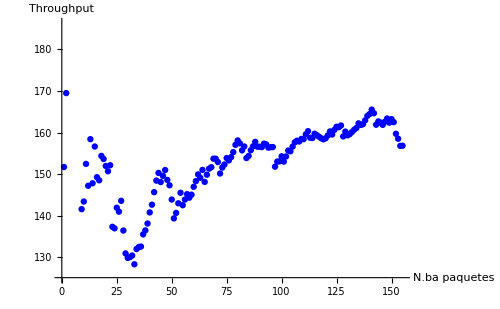
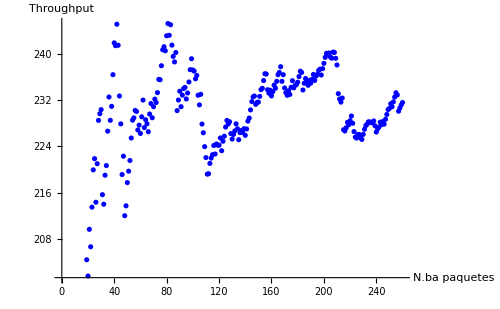
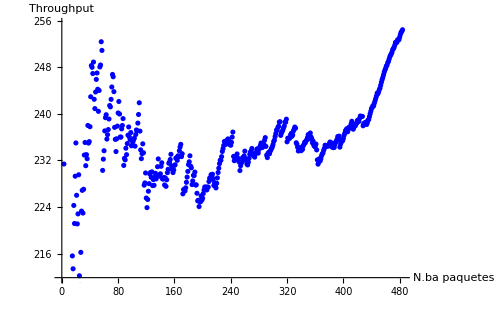
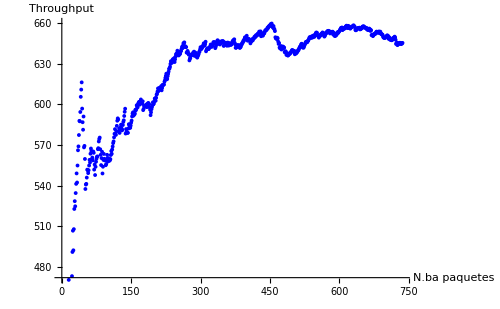
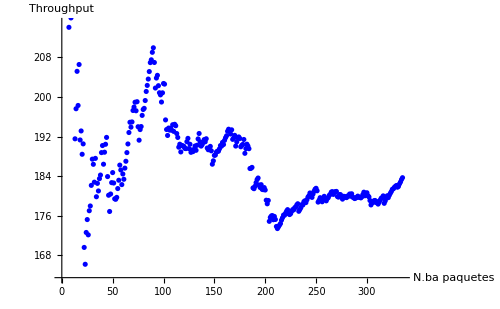
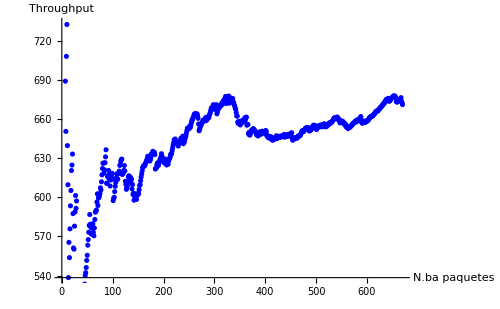
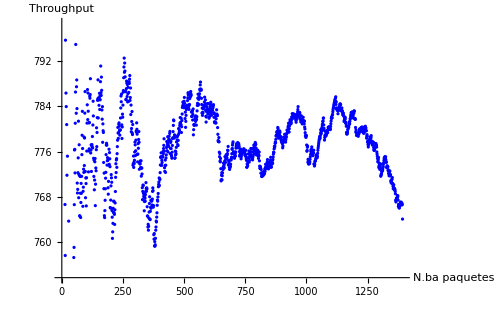
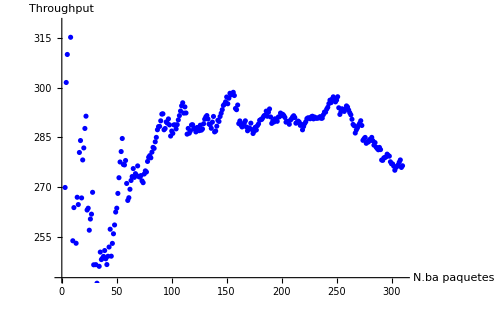
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10
```

```mathematica
ThroughputMax[paquetes123]
ThroughputMax[paquetes124]
ThroughputMax[paquetes1523]
ThroughputMax[paquetes154]
ThroughputMax[paquetes23]
ThroughputMax[paquetes24]
ThroughputMax[paquetes523]
ThroughputMax[paquetes524]
ThroughputMax[paquetes54] 
Last[paquetes123]
Last[paquetes123][[9]]
Length[paquetes123]
(Length[paquetes123]/Last[paquetes123][[1]])//N
```

156.843

183.685

231.591

645.476

670.968

764.003

276.495

332.154

859.355

{0.988249,4135.16,1325,0,0,1940,1,{Ori-1,2,3},0.984549}

0.984549

155

156.843

```mathematica
ThroughputMax[paquetes1524]
```

254.431

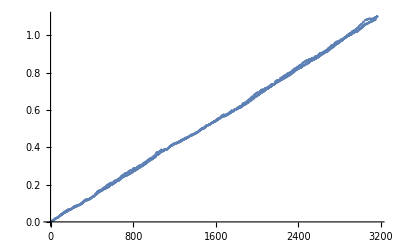

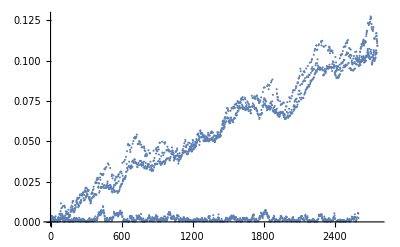

```mathematica
(*Obtencion del retardo extremo a extremo de cada paquete*)

out3;
out4;
ListPlot[Map[(#[[1]]-#[[9]])&,out3]]
ListPlot[Map[(#[[1]]-#[[9]])&,out4]]
```

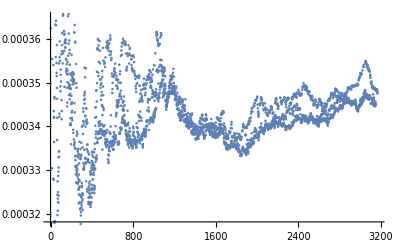

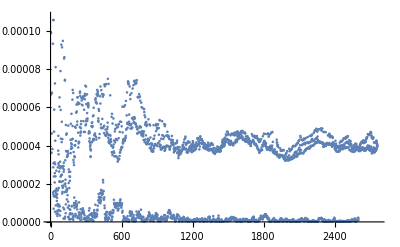

```mathematica
Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out3]]
]

Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out4]]
]
```

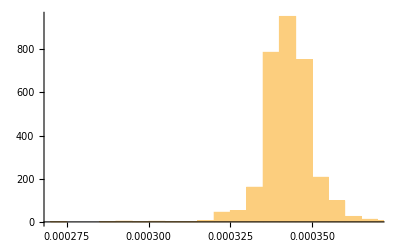

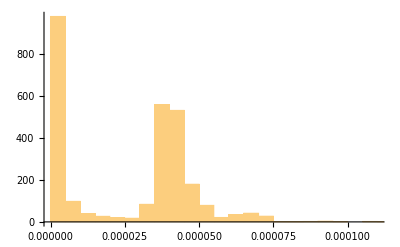

```mathematica
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out3]]
]
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out4]]
]
```

# 7B.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo S&W

```mathematica
(*Ejecución de la función*)
opcionesDistintas3SW=ObtenerOpcionesDistintas[out3SW]
opcionesDistintas4SW=ObtenerOpcionesDistintas[out4SW]

paquetes123SW = getPacketsWithRoute[out3SW,{"Ori-1",2,3}];
paquetes1523SW = getPacketsWithRoute[out3SW,{"Ori-1",5,2,3}];
paquetes1524SW = getPacketsWithRoute[out4SW,{"Ori-1",5,2,4}];
paquetes154SW = getPacketsWithRoute[out4SW,{"Ori-1",5,4}];
paquetes124SW = getPacketsWithRoute[out4SW,{"Ori-1",2,4}]; 
paquetes23SW= getPacketsWithRoute[out3SW,{"Ori-2",2,3}];
paquetes24SW = getPacketsWithRoute[out4SW,{"Ori-2",2,4}]; 
paquetes523SW = getPacketsWithRoute[out3SW,{"Ori-5",5,2,3}];
paquetes524SW = getPacketsWithRoute[out4SW,{"Ori-5",5,2,4}]; 
paquetes54SW = getPacketsWithRoute[out4SW,{"Ori-5",5,4}]; 

tot1SW = Length[out3SW]+Length[out4SW]
tot2SW = Length[paquetes123SW]+ Length[paquetes1523SW]+Length[paquetes154SW]+Length[paquetes1524SW]+ Length[paquetes124SW]+Length[paquetes23SW]+Length[paquetes24SW]+Length[paquetes523SW]+Length[paquetes524SW]+Length[paquetes54SW]
```

{{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,5,2,3},{Ori-1,2,3}}

{{Ori-2,2,4},{Ori-1,2,4},{Ori-1,5,4},{Ori-5,5,4},{Ori-5,5,2,4},{Ori-1,5,2,4}}

5921

5921

```mathematica
t123 = getRetardo[paquetes123SW]
t124= getRetardo[paquetes124SW]
t1523 = getRetardo[paquetes1523SW]
t154 = getRetardo[paquetes154SW]
t23 = getRetardo[paquetes23SW]
t24 = getRetardo[paquetes24SW]
t523 = getRetardo[paquetes523SW]
t524 = getRetardo[paquetes524SW]
t54 = getRetardo[paquetes54SW]
```

0.00349256

0.408187

0.131324

0.146675

0.00292086

0.426168

0.0928897

0.570503

0.11025

```mathematica
t1524 = getRetardo[paquetes1524SW]
```

0.643857

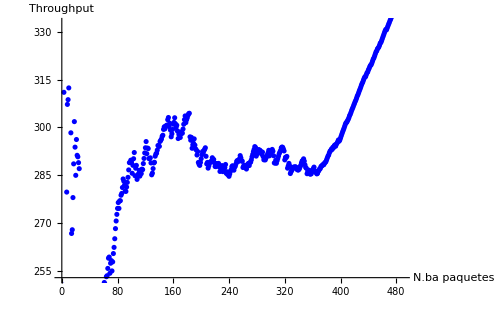
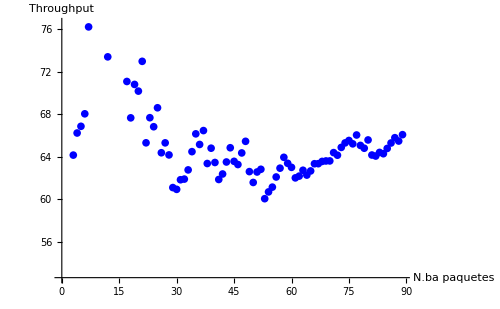
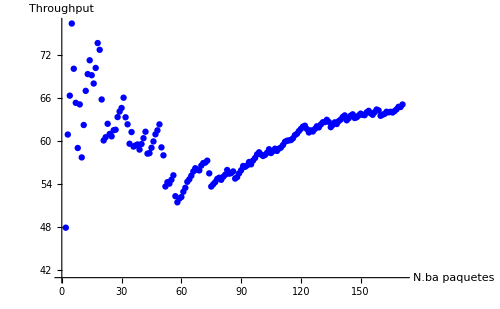
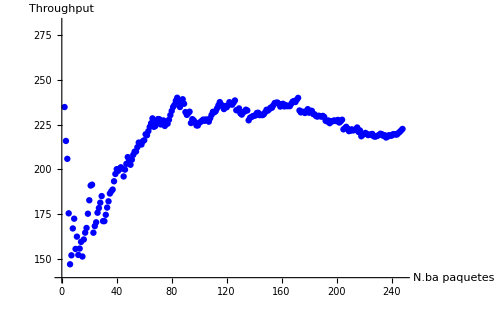
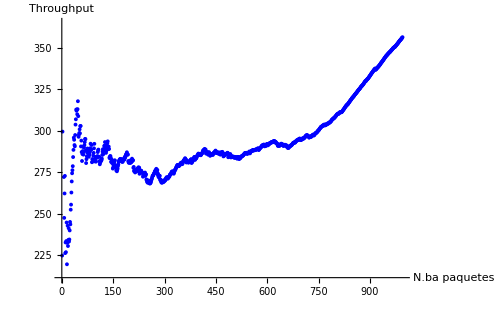
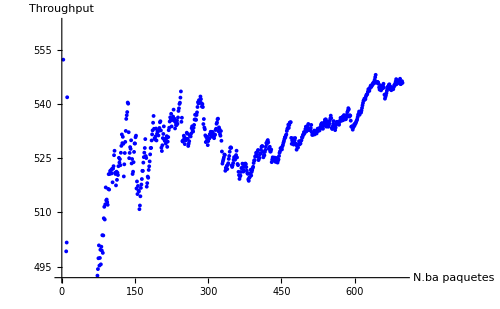
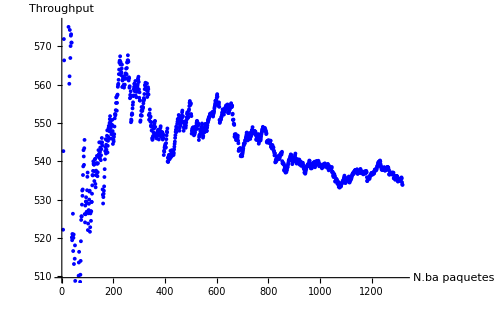
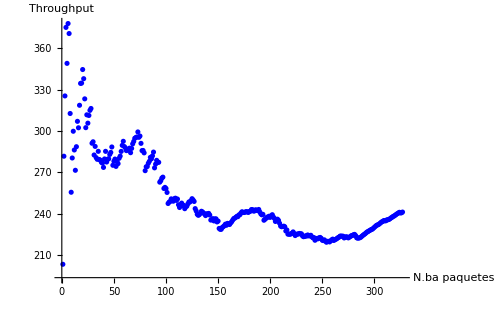
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3 | -Graphics-TH en ruta 1-5-2-4 | 
-Graphics-TH en ruta 1-5-4 | -Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3 | 
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3 | -Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54SW],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10SW=Grid[{{grafica1,grafica2, grafica3},{grafica4,grafica5, grafica6},{grafica7,grafica8, grafica9, grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10SW
```

```mathematica
ThroughputMax[paquetes123SW]
ThroughputMax[paquetes124SW]
ThroughputMax[paquetes1523SW]
ThroughputMax[paquetes154SW]
ThroughputMax[paquetes23SW]
ThroughputMax[paquetes24SW]
ThroughputMax[paquetes523SW]
ThroughputMax[paquetes524SW]
ThroughputMax[paquetes54SW]
```

157.092

171.803

202.008

612.878

650.646

722.446

275.805

346.387

806.905

```mathematica
ThroughputMax[paquetes1524SW]
```

248.411

{{0.00283787,2034.24,1,0,2,1,1,{Ori-2,2,3},0.0000974364},{0.0033808,670.728,2,0,0,2,1,{Ori-2,2,3},0.00104792},{0.0049115,566.081,3,0,2,2,1,{Ori-5,5,2,3},0.00124024},{0.00543284,601.616,4,0,0,4,1,{Ori-2,2,3},0.00236195},{0.00621128,1424.33,5,0,0,5,1,{Ori-1,2,3},0.00136951},{0.00673546,610.711,6,0,0,11,1,{Ori-2,2,3},0.00538236},{0.00709824,94.2299,7,0,0,8,1,{Ori-5,5,2,3},0.00367599},{0.00798142,1759.51,8,0,0,8,1,{Ori-1,2,3},0.0018976},{0.00922021,2897.45,9,0,0,9,1,{Ori-5,5,2,3},0.00425807},{0.00964602,295.945,10,0,0,9,1,{Ori-1,2,3},0.00212012}}

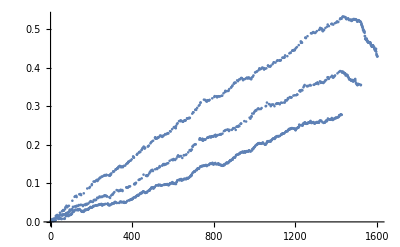

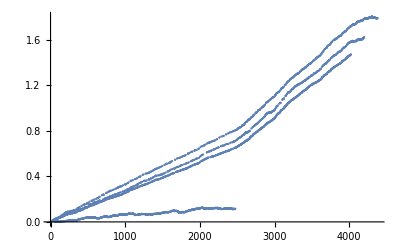

```mathematica
out3SW[[1;;10]]
out4SW;
ListPlot[Map[(#[[1]]-#[[9]])&,out3SW]]
ListPlot[Map[(#[[1]]-#[[9]])&,out4SW]]
```

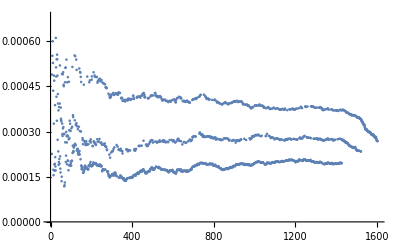

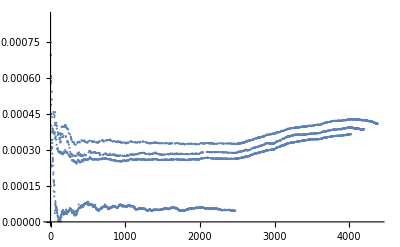

```mathematica
Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out3SW]]
]

Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out4SW]]
]
```

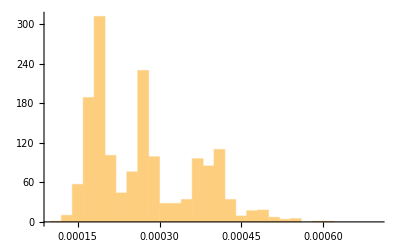

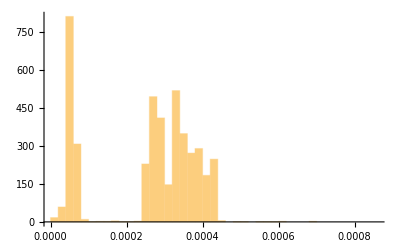

```mathematica
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out3SW]]
]
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out4SW]]
]
```

# 7C.- Obtención de estadísticas y representación gráfica de resultados parciales CON protocolo GBN

```mathematica
(*Ejecución de la función*)
opcionesDistintas3GBN=ObtenerOpcionesDistintas[out3GBN]
opcionesDistintas4GBN=ObtenerOpcionesDistintas[out4GBN]

paquetes123GBN = getPacketsWithRoute[out3GBN,{"Ori-1",2,3}];
paquetes1523GBN = getPacketsWithRoute[out3GBN,{"Ori-1",5,2,3}];
paquetes1524GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,2,4}];
paquetes154GBN = getPacketsWithRoute[out4GBN,{"Ori-1",5,4}];
paquetes124GBN = getPacketsWithRoute[out4GBN,{"Ori-1",2,4}]; 
paquetes23GBN= getPacketsWithRoute[out3GBN,{"Ori-2",2,3}];
paquetes24GBN = getPacketsWithRoute[out4GBN,{"Ori-2",2,4}]; 
paquetes523GBN = getPacketsWithRoute[out3GBN,{"Ori-5",5,2,3}];
paquetes524GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,2,4}]; 
paquetes54GBN = getPacketsWithRoute[out4GBN,{"Ori-5",5,4}]; 

tot1GBN = Length[out3GBN]+Length[out4GBN]
tot2GBN = Length[paquetes123GBN]+ Length[paquetes1523GBN]+Length[paquetes154GBN]+Length[paquetes1524GBN]+ Length[paquetes124GBN]+Length[paquetes23GBN]+Length[paquetes24GBN]+Length[paquetes523GBN]+Length[paquetes524GBN]+Length[paquetes54GBN]
```

{{Ori-2,2,3},{Ori-5,5,2,3},{Ori-1,5,2,3},{Ori-1,2,3}}

{{Ori-2,2,4},{Ori-1,2,4},{Ori-5,5,4},{Ori-1,5,4},{Ori-1,5,2,4},{Ori-5,5,2,4}}

5878

5878

```mathematica
t123 = getRetardo[paquetes123GBN]
t124= getRetardo[paquetes124GBN]
t1523 = getRetardo[paquetes1523GBN]
t154 = getRetardo[paquetes154GBN]
t23 = getRetardo[paquetes23GBN]
t24 = getRetardo[paquetes24GBN]
t523 = getRetardo[paquetes523GBN]
t524 = getRetardo[paquetes524GBN]
t54 = getRetardo[paquetes54GBN]
```

0.0168509

0.00168771

0.0177152

0.00210744

0.0156885

0.0010249

0.0166143

0.00198862

0.00118649

```mathematica
t1524 = getRetardo[paquetes1524GBN]
```

0.00299757

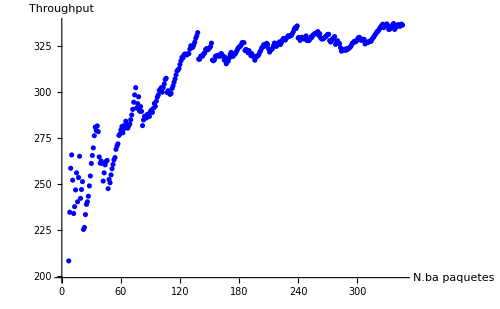
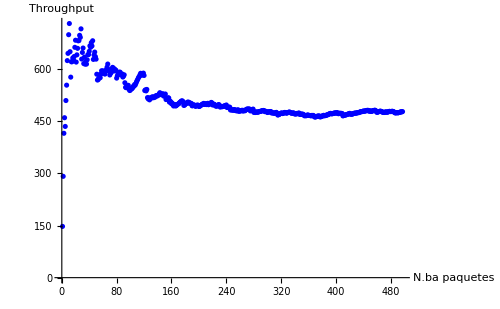
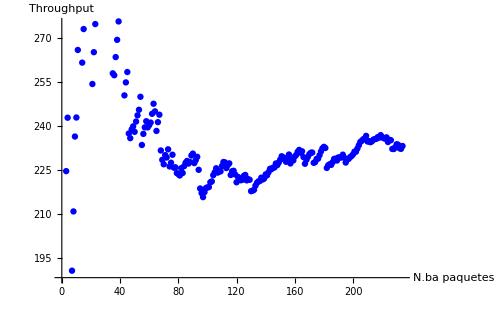
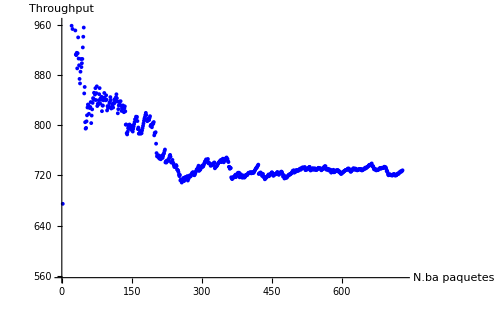
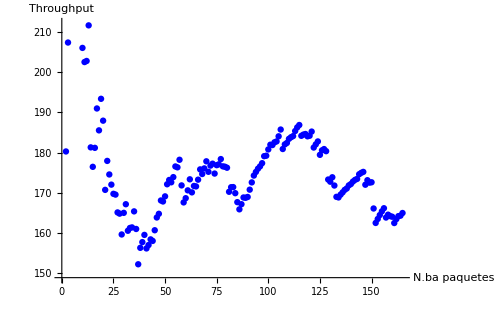
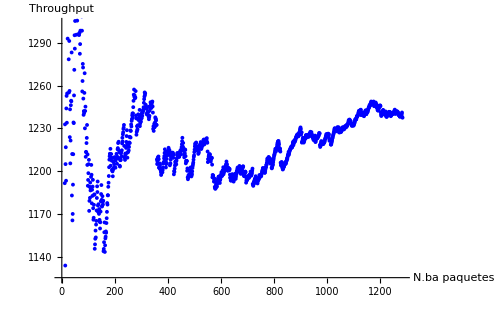
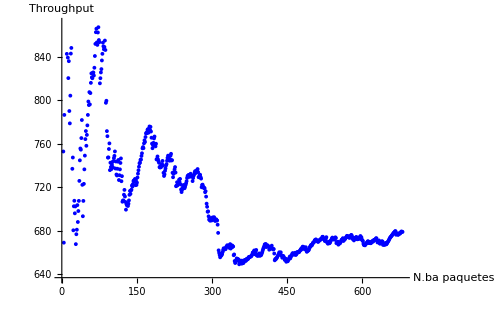
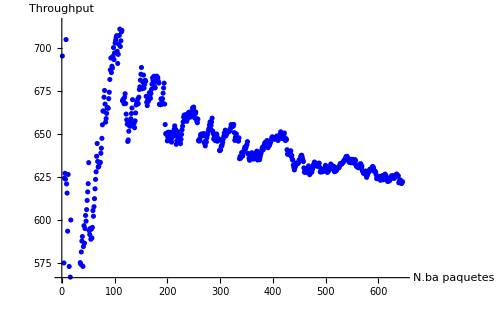
-Graphics-TH en ruta 1-2-3 | -Graphics-TH en ruta 1-5-2-3
-Graphics-TH en ruta 1-5-2-4 | -Graphics-TH en ruta 1-5-4
-Graphics-TH en ruta 1-2-4 | -Graphics-TH en ruta 2-3
-Graphics-TH en ruta 2-4 | -Graphics-TH en ruta 5-2-3
-Graphics-TH en ruta 5-2-4 | -Graphics-TH en ruta 5-4

```mathematica
(*Gráficas con ListPlot y etiquetas usando Labeled*)
grafica1=Labeled[ListPlot[ThroughputList[paquetes123GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-3"];
grafica2=Labeled[ListPlot[ThroughputList[paquetes1523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-3"];
grafica3=Labeled[ListPlot[ThroughputList[paquetes1524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-2-4"];
grafica4=Labeled[ListPlot[ThroughputList[paquetes154GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-5-4"];
grafica5=Labeled[ListPlot[ThroughputList[paquetes124GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 1-2-4"];
grafica6=Labeled[ListPlot[ThroughputList[paquetes23GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-3"];
grafica7=Labeled[ListPlot[ThroughputList[paquetes24GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 2-4"];
grafica8=Labeled[ListPlot[ThroughputList[paquetes523GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-3"];
grafica9=Labeled[ListPlot[ThroughputList[paquetes524GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-2-4"];
grafica10=Labeled[ListPlot[ThroughputList[paquetes54GBN],ImageSize->{500,500},PlotStyle->Blue,AxesLabel->{"N.ba paquetes","Throughput"}],"TH en ruta 5-4"];

(*Crear la tabla con 5 filas y 2 columnas*)
tablaListPlot10GBN=Grid[{{grafica1,grafica2},{grafica3,grafica4},{grafica5,grafica6},{grafica7,grafica8},{grafica9,grafica10}},
ItemSize->{Automatic,Automatic},(*10 unidades de ancho para las celdas*)
Frame->All];

(*Mostrar la tabla*)
tablaListPlot10GBN
```

```mathematica
ThroughputMax[paquetes123GBN]
ThroughputMax[paquetes124GBN]
ThroughputMax[paquetes1523GBN]
ThroughputMax[paquetes154GBN]
ThroughputMax[paquetes23GBN]
ThroughputMax[paquetes24GBN]
ThroughputMax[paquetes523GBN]
ThroughputMax[paquetes524GBN]
ThroughputMax[paquetes54GBN]
```

336.383

165.007

478.094

728.261

1237.53

678.997

622.15

367.62

928.871

```mathematica
ThroughputMax[paquetes1524GBN]
```

233.185

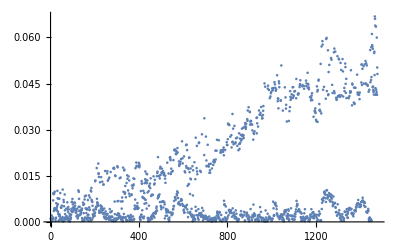

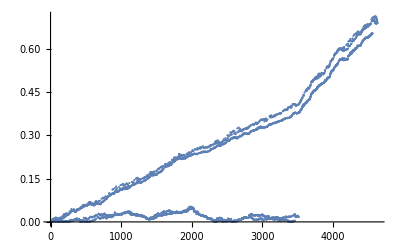

```mathematica
out3GBN[[1;;100]];
out4GBN;
ListPlot[Map[(#[[1]]-#[[9]])&,out3GBN]]
ListPlot[Map[(#[[1]]-#[[9]])&,out4GBN]]
```

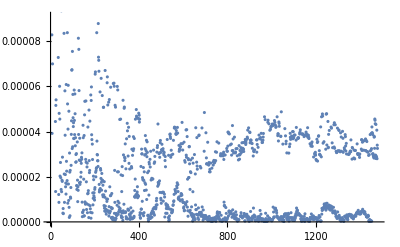

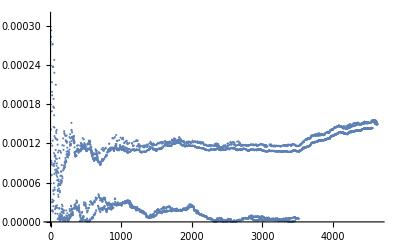

```mathematica
Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out3GBN]]
]

Module[{n=1},
ListPlot[Map[((#[[1]]-#[[9]])/n++)&,out4GBN]]
]
```

```mathematica
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out3]]
]
Module[{n=1},
Histogram[Map[((#[[1]]-#[[9]])/n++)&,out4]]
]
```

-Graphics-

-Graphics-